```mathematica
Clear["W`ICA`*"]
<<ICA`;
<<matcher`;
Needs["StatisticalPlots`"]
Names["W`ICA`*"]
```

{Epsilon,fastICA,maxNumIterations,retW,Whiten}

```mathematica
(* build a set of sample*)
mu1=Table[i,{i,50}];
mu2=Table[-i,{i,50}];
sgm=DiagonalMatrix[Table[0.1,{i,50}]];
s1=RandomVariate[MultinormalDistribution[mu1,sgm],5];
s2=RandomVariate[MultinormalDistribution[mu2,sgm],5];
Dimensions[s2]
```

{5,50}

```mathematica
sample=Join[s1,s2];
```

```mathematica
(*Export["..\\tmp\\sample.mat",sample]*)
```

..\tmp\sample.mat

```mathematica
(*sample=Join[s1,s2];
cs1=Chop[Standardize[sample,Mean,1&]];

Chop[Covariance[cs1]*9-cs1ᵀ.cs1]
Correlation[cs1]
*)
(*cs1=Chop[Standardize[s1,Mean]];*)
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

{{1.,0.937224,0.946581,0.97186,0.968636},{0.937224,1.,0.981601,0.981541,0.984707},{0.946581,0.981601,1.,0.989978,0.994321},{0.97186,0.981541,0.989978,1.,0.997074},{0.968636,0.984707,0.994321,0.997074,1.}}

```mathematica
(*Variance[cs1]
Diagonal[Covariance[cs1]]
Diagonal[cs1ᵀ.cs1/9]*)
```

{1.15894,5.39943,10.1264,18.7601,27.8712}

{1.15894,5.39943,10.1264,18.7601,27.8712}

{1.15894,5.39943,10.1264,18.7601,27.8712}

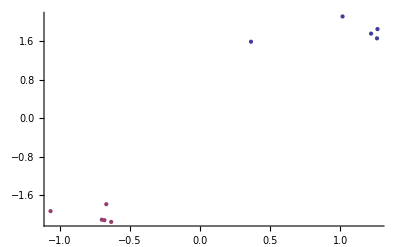

```mathematica
ListPlot[{s1[[;;,;;2]],s2[[;;,;;2]]}]
```

```mathematica
sample=Join[s1,s2];

Dimensions[sample]
```

{10,50}

```mathematica
{dd,ds}=eucDist[{s1,s2}];
```

```mathematica
dd
ds
```

{413.742,413.798,413.669,414.109,413.97,414.051,414.106,413.982,414.421,414.28,414.28,414.334,414.206,414.647,414.51,414.392,414.446,414.32,414.761,414.621,414.385,414.438,414.313,414.753,414.614}

{2.46808,2.74954,3.17087,2.85874,2.74178,3.40547,3.25671,3.62271,3.11882,3.28812,3.26554,3.4209,3.58965,2.90702,3.07997,2.90986,3.36583,2.29681,3.11467,3.27931}

```mathematica
{ic,W,A}=fastICA[sampleᵀ,retW->True];(* we want independent features, so each line is a feature, each column is a measure*)
```

use deltaW:1/1000, Maxstep:100

using opimized method for whiten

Dimension adjusted to 9 according to covariance matrix

Sum of 41 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

Smallest remaining (non-zero) eigenvalue 0.235806

Largest remaining (non-zero) eigenvalue 47673.7

whiten OK

guess OK

total time:0.21875seconds

ICs computation successed!

```mathematica
ic//MatrixForm
```

(0.50652 | 0.506521 | -2.65575 | 0.506521 | 0.506531 | 0.50652 | 0.506532 | 0.506521 | 0.506521 | 0.50652
-0.658891 | -0.658891 | -0.305552 | -0.658891 | -0.658892 | -0.660588 | -0.658893 | 2.52288 | -0.658891 | -0.658891
-0.55918 | -0.559567 | -0.158411 | 2.64786 | -0.559181 | -0.55944 | -0.559182 | -0.158622 | -0.55918 | -0.55918
-0.655985 | -0.657581 | -0.192998 | -0.19301 | -0.65566 | 2.58426 | -0.655568 | -0.191513 | -0.655388 | -0.656498
0.488046 | 0.492653 | -0.0587009 | -0.0586277 | -2.79739 | -0.0582409 | 0.487942 | -0.058694 | 0.487894 | 0.488177
0.873327 | -2.4796 | 0.202638 | 0.202313 | 0.199133 | 0.201258 | 0.878046 | 0.202636 | 0.873044 | 0.87357
0.0177995 | 0.0254504 | 0.0224915 | 0.0224838 | 0.022436 | 0.0218755 | 2.14754 | 0.0224831 | 0.0173497 | -2.09508
2.66572 | 0.0663518 | 0.0676055 | 0.0676089 | 0.067618 | 0.0677356 | -0.811265 | 0.0676091 | -0.764789 | -0.818107
-0.239134 | -0.271934 | -0.273817 | -0.273821 | -0.273776 | -0.27333 | 0.933352 | -0.273821 | -2.73545 | 0.943519)

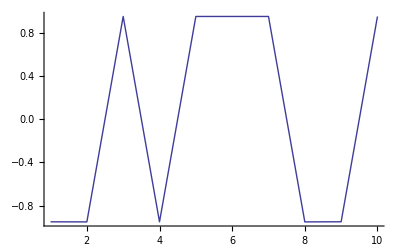
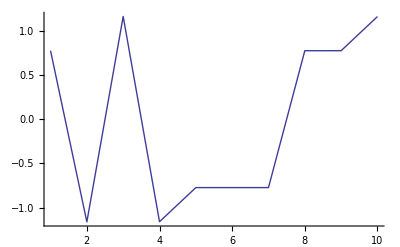
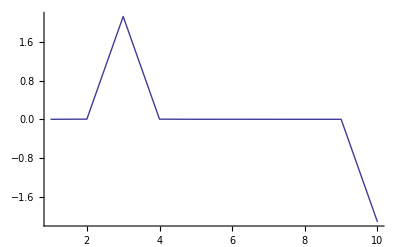
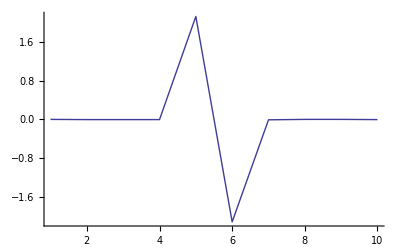
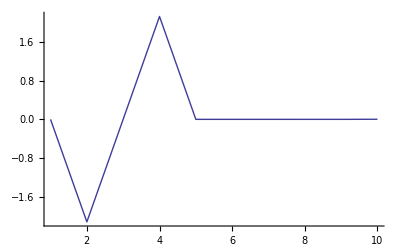
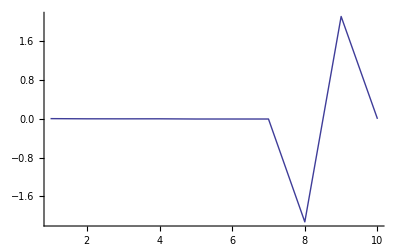
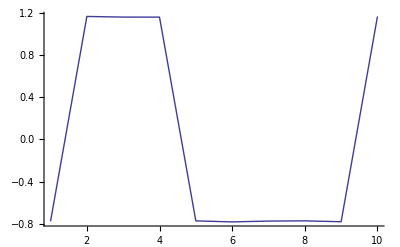
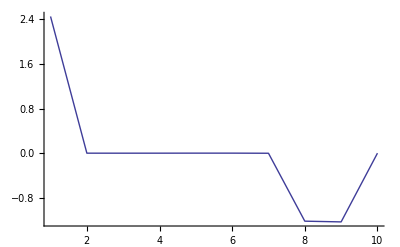

```mathematica
Table[ListPlot[ic[[i]],Joined->True],{i,Length[ic]}]
```

```mathematica
Dimensions[ic]
```

{5,10}

```mathematica
iss0=Transpose[ic];
iss1={iss0[[;;5]],iss0[[6;;]]};
```

```mathematica
Dimensions[iss1]
```

{2,5,9}

```mathematica
{dd,ds}=eucDist[iss1];
```

```mathematica
dd
ds
```

{4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264}

{4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264,4.24264}

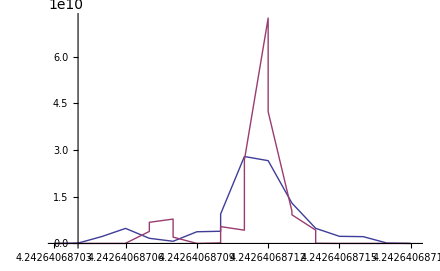

```mathematica
SmoothHistogram[{dd,ds}]
```

```mathematica
(* matlab result*)
```

```mathematica
ssi=Import["..\\tmp\\ss_i.mat"][[1]];
```

```mathematica
Dimensions[ssi]
iss0=Transpose[ssi];
iss1={iss0[[;;5]],iss0[[6;;]]};
```

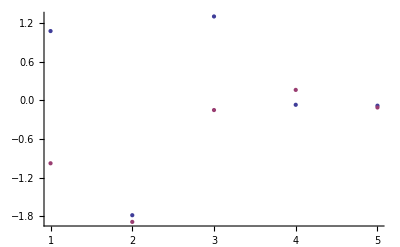

```mathematica
ListPlot[iss1[[;;,;;,5]]]
```

```mathematica
{dd,ds}=eucDist[iss1[[;;,;;,4]]]
```

{{1.34851,1.34937,1.33889,1.22238,0.654174,2.08275,2.08361,2.07313,1.95662,1.38841,0.250561,0.251417,0.240935,0.124428,0.443778,2.8287,2.82956,2.81908,2.70257,2.13436,2.00203,2.00289,1.99241,1.8759,1.30769},{0.73424,1.09795,1.48019,0.653521,1.83219,0.745949,0.0807189,2.57814,1.75147,0.826668,0.000856055,0.00962591,0.126132,0.694339,0.010482,0.126989,0.695195,0.116507,0.684713,0.568206}}

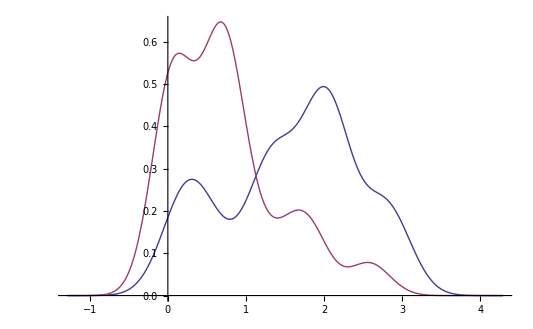

```mathematica
SmoothHistogram[{dd,ds}]
```

```mathematica
Chop[Covariance[icᵀ]]//MatrixForm
```

(1.11111 | 0 | 0 | 0 | 0
0 | 1.11111 | 0 | 0 | 0
0 | 0 | 1.11111 | 0 | 0
0 | 0 | 0 | 1.11111 | 0
0 | 0 | 0 | 0 | 1.11111)

```mathematica
Chop[Correlation[icᵀ]]
```

{{1.,0,0,0,0},{0,1.,0,0,0},{0,0,1.,0,0},{0,0,0,1.,0},{0,0,0,0,1.}}

## for normal dist data, PCA and ICA seems same

```mathematica
(*this dataset*)
s1=RandomVariate[MultinormalDistribution[{1,1,2},{{1,0,0},{0,1,0},{0,0,1}}],20];
s2=RandomVariate[MultinormalDistribution[{-1,-1,-1},{{1,0,0},{0,1,0},{0,0,1}}],20];
ListPlot3D[{s1,s2},Mesh->None];
```

```mathematica
sample=Join[s1,s2];
```

```mathematica
pc=PrincipalComponents [sample];
Dimensions[pc]
```

{40,3}

```mathematica
pcᵀ.pc
```

{{1915.96,-2.15805×10^-13,1.65723×10^-13},{-2.15805×10^-13,402.415,4.39821×10^-14},{1.65723×10^-13,4.39821×10^-14,367.808}}

```mathematica
Chop[Correlation[pc]]
```

{{1.,0,0},{0,1.,0},{0,0,1.}}

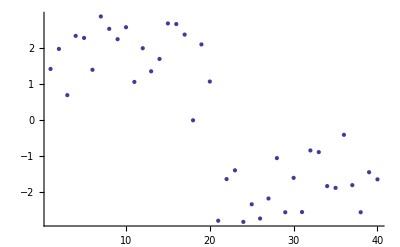

```mathematica
ListPlot[pc[[;;,1]]]
```

```mathematica
Mean[pc]
```

{7.35523×10^-17,-7.26762×10^-17,-5.40366×10^-18}

```mathematica
ic=fastICA[sampleᵀ];
Dimensions[ic]
```

use deltaW:1/1000, Maxstep:100

Smallest remaining (non-zero) eigenvalue 1.09944

Largest remaining (non-zero) eigenvalue 4.10649

whiten OK

guess OK

total time:0.109375seconds

ICs computation successed!

{3,40}

```mathematica
ListPlot3D[Partition[icᵀ,100]]
```

-Graphics3D-

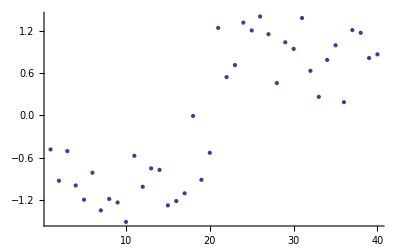

```mathematica
ListPlot[icᵀ[[;;,2]]]
```

```mathematica
k4[ic[[1]]]
```

-1.24848

{2,200,3}

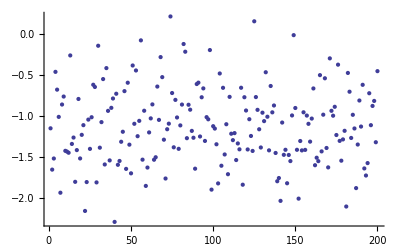

```mathematica
Dimensions[Partition[icᵀ,200]]
ListPlot[Partition[icᵀ,200][[1,;;,2]]]
```

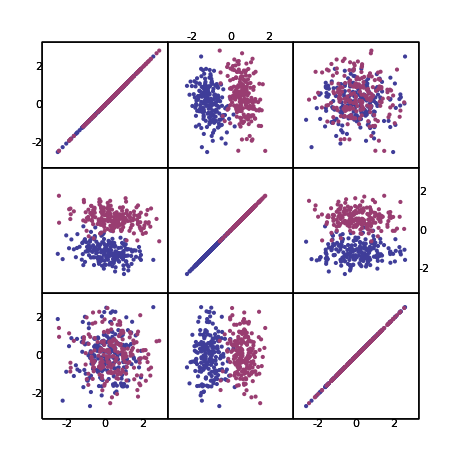

```mathematica
ScatterPlot[Partition[icᵀ,200],{{-3,3},{-3,3}}]
```

Now input pc as sample to ica

```mathematica
icp=fastICA[pcᵀ]ᵀ;
Dimensions[icp]
```

use deltaW:1/1000, Maxstep:100

Smallest remaining (non-zero) eigenvalue 0.910432

Largest remaining (non-zero) eigenvalue 4.91355

Sum of 0 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

whiten OK

guess OK

total time:0.109375seconds

{400,3}

```mathematica
ListPlot3D[Partition[icp,100]]
```

-Graphics3D-

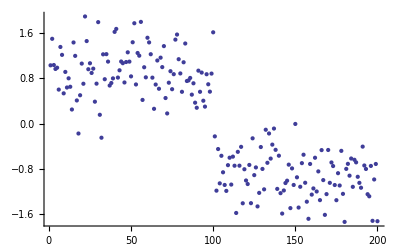

```mathematica
ListPlot[icp[[;;,1]]]
```

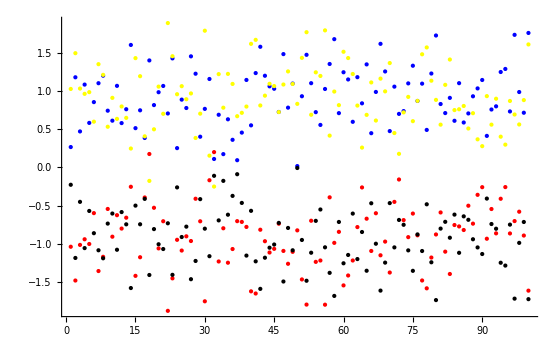

```mathematica
sic=Partition[icᵀ,100][[All,;;,1]];
sicp=Partition[icp,100][[All,;;,1]];
Show[ListPlot[sic,PlotStyle->{Red,Blue}],ListPlot[sicp,PlotStyle->{Yellow,Black}]]
```

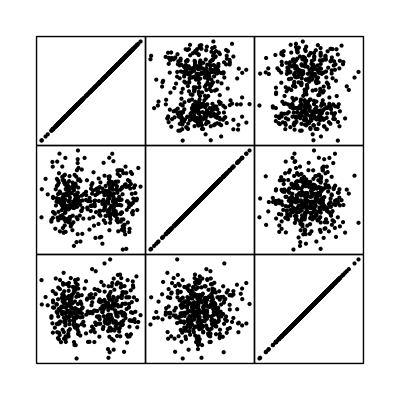

```mathematica
PairwiseScatterPlot[icp]
```

```mathematica
(* compare*)
Length[Select[sic[[1]],#>0&]]+Length[Select[sic[[2]],#<0&]]
Length[Select[sicp[[1]],#<0&]]+Length[Select[sicp[[2]],#>0&]]
```

2

2

```mathematica
(*now try matlab*)
Export["..\\tmp\\s100.mat",sample];
```

```mathematica
ssi=Import["..\\tmp\\s100_i.mat"][[1]];
```

```mathematica
(* the result looks the same*)
```

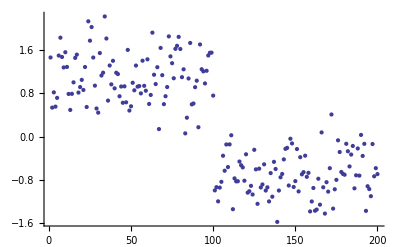

```mathematica
ListPlot[ssiᵀ[[;;,1]]]
```

## try T dist,same

```mathematica
s1=RandomVariate[MultivariateTDistribution[{1,1,2},{{1,0,0},{0,1,0},{0,0,1}},3],100];
s2=RandomVariate[MultivariateTDistribution[{-11,-11,-11},{{1,0,0},{0,1,0},{0,0,1}},3],100];
```

```mathematica
sample2=Join[s1,s2];
```

```mathematica
ListPointPlot3D[sample2]
```

-Graphics3D-

```mathematica
pc=PrincipalComponents [sample2];
Dimensions[pc]
```

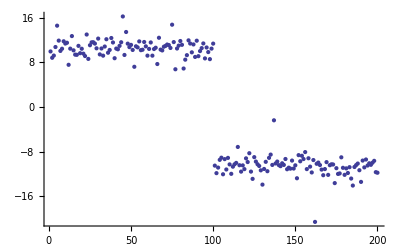

```mathematica
ListPlot[pc[[;;,1]]]
```

```mathematica
ic=fastICA[sample2ᵀ,10^-3,100];
Dimensions[ic]
```

whiten OK

guess OK

IC 1 computed in 4 steps

IC 2 computed in 4 steps

IC 3 computed in 1 steps

Independent Components Correlation Matrix=  | IC 1 | IC 2 | IC 3
IC 1 | 1. | 0 | 0
IC 2 | 0 | 1. | 0
IC 3 | 0 | 0 | 1.

{3,200}

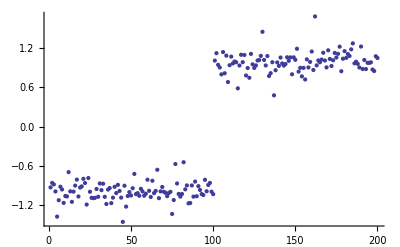

```mathematica
ListPlot[icᵀ[[;;,1]]]
```

## try Sin data

```mathematica
s1=Table[Sin[0.5i],{i,100}];
s2=Table[Sin[8 i],{i,100}];
```

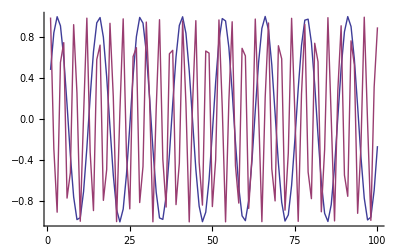

```mathematica
ListPlot[{s1,s2},Joined->True]
```

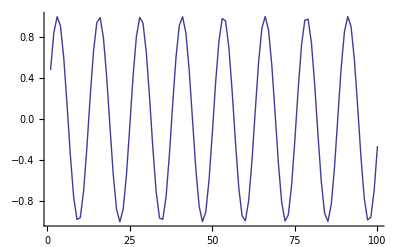

```mathematica
ListPlot[s1,Joined->True]
```

```mathematica
sss={s1,s2}//N;(* there must be N, or slower...*)
Dimensions[sss]
Correlation[sssᵀ]
```

{2,100}

{{1.,0.000569751},{0.000569751,1.}}

```mathematica
(*mixing m*)
m=({{0.8, 0.2}, {0.1, 0.9}});
sm=m.{s1,s2};
Dimensions[sm]
```

{2,100}

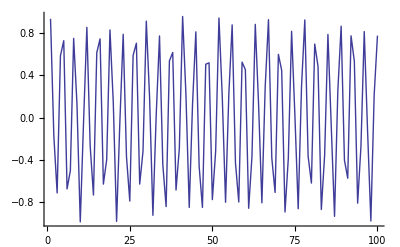

```mathematica
ListPlot[sm[[2]],Joined->True]
```

```mathematica
(*separate sm*)
{ic,W,A}=fastICA[sm,retW->True];
```

use deltaW:1/1000, Maxstep:100

Smallest remaining (non-zero) eigenvalue 0.244103

Largest remaining (non-zero) eigenvalue 0.518444

Sum of 0 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

whiten OK

guess OK

total time:0.09375seconds

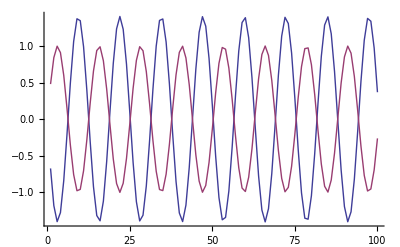

```mathematica
ListPlot[{ic[[2]],s1},Joined->True]
```

```mathematica
A.W
W.A
```

{{1.,-6.87384×10^-17},{-4.49266×10^-17,1.}}

{{1.,6.24297×10^-17},{2.66172×10^-17,1.}}

```mathematica
W[[2]].sm==ic[[2]]
```

True

```mathematica
A.ic==sm
```

True

```mathematica
Dimensions[ic]
```

{2,100}

```mathematica
A/Total[Abs[A]]
```

{{0.182048,-0.7264},{1.00075,-0.11126}}

```mathematica
A
```

{{0.142641,-0.570128},{0.641892,-0.0716229}}

```mathematica
Correlation[icᵀ]
```

{{1.,-9.19921×10^-17},{-9.19921×10^-17,1.}}

```mathematica
p=sm[[2]].icᵀ
```

{63.5645,-7.06442}

```mathematica
p/Total[Abs[p]]
```

{0.899978,-0.100022}

```mathematica
(*sample projection is equivalent to mixing matrix*)
```

```mathematica
sm.icᵀ/A
```

{{99.0173,98.9997},{99.0225,98.9881}}

```mathematica
ic.icᵀ
```

{{99.0226,0.0013296},{0.0013296,99.0001}}

## test new whiten

```mathematica
cc=Standardize[smᵀ,Mean,1&]ᵀ;
Mean[ccᵀ]
```

{-1.0339×10^-17,-5.37764×10^-18}

```mathematica
{d1,e1}=Eigensystem[Covariance[ccᵀ]]
```

{{0.518444,0.244103},{{0.607626,0.794223},{-0.794223,0.607626}}}

```mathematica
{d2,e2}=Eigensystem[Covariance[cc]]
```

{{24.639,2.4869×10^-14,-3.6806×10^-15,1.53705×10^-15,-3.52329×10^-16,«91»,5.34041×10^-20,5.00282×10^-20,-4.53402×10^-20,-3.10792×10^-20},{«1»}}

```mathematica
Dimensions[e1.cc]
Dimensions[e2]
```

{2,100}

{100,100}

```mathematica
{ww,dd}=Whiten[cc];
```

2

Smallest remaining (non-zero) eigenvalue 0.244103

Largest remaining (non-zero) eigenvalue 0.518444

```mathematica
ww
```

{{0.120668,-0.161323}}

```mathematica
Chop[Eigensystem[Covariance[ss]]]
```

{{1348.71,1109.06,1060.26,985.642,826.003,759.366,742.479,625.669,590.994,488.287},{{-0.202934,0.511999,-0.0193299,-0.285683,0.0325139,0.0243577,-0.31886,-0.585983,-0.391734,-0.120556},{0.269047,0.273261,0.622135,-0.278315,-0.29081,-0.167959,0.456565,0.0712389,-0.176797,0.17569},{0.237964,0.0468587,-0.486656,-0.281112,-0.351311,0.64101,0.238687,0.0783113,-0.153798,0.065187},{-0.351094,-0.0569114,-0.176042,-0.248796,0.149558,-0.100324,0.225483,-0.238849,0.24292,0.762411},{0.295026,-0.618052,0.0206211,-0.504778,0.366675,-0.108466,0.0340878,-0.191161,-0.26826,-0.140933},{0.124929,-0.0615812,-0.4037,0.373904,-0.239384,-0.469999,0.44542,-0.383229,-0.198947,-0.121556},{-0.417171,-0.385767,0.133521,-0.251242,-0.679766,-0.0612015,-0.123731,-0.143362,0.212002,-0.222637},{-0.544664,-0.219711,0.230149,0.2816,0.147536,0.346189,0.336849,0.0411439,-0.515006,-0.0282138},{0.112688,-0.182656,-0.0522517,0.139462,-0.294573,-0.191456,-0.487428,0.228964,-0.528721,0.488644},{-0.347133,0.203761,-0.328366,-0.37885,0.0787912,-0.396644,0.127043,0.574709,-0.177084,-0.21285}}}

### so the opt method

```mathematica
(* a matrix*)
ss=Table[RandomReal[{0,100},10],{50}];
ss=Standardize[ssᵀ,Mean,1&]ᵀ;
Dimensions[ss]
```

{50,10}

```mathematica
Mean[ssᵀ];
```

{-1.77636×10^-15,-3.55271×10^-16,-2.84217×10^-15,-7.10543×10^-16,-2.13163×10^-15,2.84217×10^-15,-1.13687×10^-14,-1.06581×10^-15,1.42109×10^-15,2.84217×10^-15,-3.90799×10^-15,2.13163×10^-15,1.42109×10^-15,2.13163×10^-15,-1.77636×10^-15,-4.26326×10^-15,-8.52651×10^-15,-1.42109×10^-15,-7.81597×10^-15,2.13163×10^-15,3.90799×10^-15,2.84217×10^-15,-1.42109×10^-15,-1.42109×10^-15,-1.42109×10^-15,-9.9476×10^-15,-1.06581×10^-15,4.9738×10^-15,-4.26326×10^-15,-4.61853×10^-15,7.10543×10^-16,2.84217×10^-15,0.,-2.84217×10^-15,0.,-2.13163×10^-15,1.42109×10^-15,-2.4869×10^-15,1.77636×10^-15,4.26326×10^-15,3.55271×10^-15,1.06581×10^-15,-2.4869×10^-15,-7.81597×10^-15,5.68434×10^-15,0.,5.68434×10^-15,-4.9738×10^-15,7.10543×10^-16,1.42109×10^-15}

```mathematica
(* first, get eigensystem as usual*)
{d,e}=Eigensystem[Covariance[ssᵀ]];
Chop[d]
e;
Dimensions[e]
```

{8144.42,7097.38,5765.4,4888.24,4678.94,4254.26,3245.81,2674.64,1802.38,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{50,50}

```mathematica
(*as the definition*)
Chop[Covariance[ssᵀ].eᵀ-eᵀ.DiagonalMatrix[d]];
```

```mathematica
(* then another way*)
{d1,e1}=Chop[Eigensystem[ssᵀ.ss/(Length[ss[[1]]]-1)]];
```

```mathematica
(* eigenvalues are the same*)
d1
e1;
```

{8144.42,7097.38,5765.4,4888.24,4678.94,4254.26,3245.81,2674.64,1802.38,0}

```mathematica
Chop[Eigensystem[Covariance[ss]][[1]]*(Length[ss]-1)/(Length[ss[[1]]]-1)]
```

{7263.19,6831.22,5531.97,5063.17,4148.68,3772.67,3119.92,2318.54,2001.64,0}

```mathematica
Chop[ssᵀ.ss.e1ᵀ/(Length[ss[[1]]]-1)-e1ᵀ.DiagonalMatrix[d1]];
```

```mathematica
(* how to find first eig using the above result?*)
```

```mathematica
(*Cov of ssᵀ is ss.ssᵀ/(Length[ss[[1]]]-1),so we have*)
(* so then*)
Chop[ss.ssᵀ.ss.e1ᵀ/(Length[ss[[1]]]-1)-ss.e1ᵀ.DiagonalMatrix[d1],10^-7];
```

```mathematica
(* and here we go*)
uu=(ss.e1ᵀ)ᵀ;
Chop[ss.ssᵀ.uuᵀ/(Length[ss[[1]]]-1)-uuᵀ.DiagonalMatrix[d1],10^-9];
```

```mathematica
Dimensions[uu]
Chop[Covariance[ssᵀ].uuᵀ-uuᵀ.DiagonalMatrix[d1],10^-9];
```

{10,50}

```mathematica
Chop[uu.uuᵀ]
```

{{73299.7,0,0,0,0,0,0,0,0,0},{0,63876.5,0,0,0,0,0,0,0,0},{0,0,51888.6,0,0,0,0,0,0,0},{0,0,0,43994.2,-1.01417×10^-10,0,0,0,0,0},{0,0,0,-1.01417×10^-10,42110.4,0,0,0,0,0},{0,0,0,0,0,38288.4,0,0,0,0},{0,0,0,0,0,0,29212.3,0,0,0},{0,0,0,0,0,0,0,24071.8,0,0},{0,0,0,0,0,0,0,0,16221.4,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
(* the new uu and original e*)
Dimensions[e]
nuu=Map[Normalize[#]&,Chop[uu]];
e[[;;9]]/uu[[;;9]];
e[[;;9]]/nuu[[;;9]];
e[[2]]/nuu[[2]];
```

{50,50}

```mathematica
(* the sign...*)
e[[;;5,;;3]]
nuu[[;;5,;;3]]
```

```mathematica
Chop[nuuᵀ.DiagonalMatrix[d][[;;10]]][[;;9,;;9]]
Chop[eᵀ.DiagonalMatrix[d]][[;;9,;;9]]
```

{{937.461,870.72,277.034,-479.384,-587.413,-278.994,-839.152,-651.05,-136.984},{940.989,-624.648,512.248,-32.904,139.479,-125.868,-716.148,-18.2844,-316.906},{1480.25,407.415,116.274,-1157.94,184.742,476.274,180.273,-400.383,-258.14},{-476.34,-996.259,1493.76,950.691,170.4,1178.77,-264.539,476.509,286.995},{-2288.56,-1076.41,-578.003,572.898,358.11,616.429,-364.541,-382.926,41.1795},{278.454,-239.181,-337.385,826.399,1241.35,1412.24,18.1488,-132.044,219.333},{-1884.81,815.178,1895.22,462.701,16.652,-548.318,241.018,66.4987,-96.0146},{310.963,618.559,888.868,829.481,527.106,88.3418,522.233,317.116,-209.36},{-2139.66,15.1399,7.53901,-12.3273,-475.934,26.312,893.411,296.158,-435.349}}

{{-937.461,870.72,277.034,479.384,587.413,-278.994,839.152,-651.05,136.984},{-940.989,-624.648,512.248,32.904,-139.479,-125.868,716.148,-18.2844,316.906},{-1480.25,407.415,116.274,1157.94,-184.742,476.274,-180.273,-400.383,258.14},{476.34,-996.259,1493.76,-950.691,-170.4,1178.77,264.539,476.509,-286.995},{2288.56,-1076.41,-578.003,-572.898,-358.11,616.429,364.541,-382.926,-41.1795},{-278.454,-239.181,-337.385,-826.399,-1241.35,1412.24,-18.1488,-132.044,-219.333},{1884.81,815.178,1895.22,-462.701,-16.652,-548.318,-241.018,66.4987,96.0146},{-310.963,618.559,888.868,-829.481,-527.106,88.3418,-522.233,317.116,209.36},{2139.66,15.1399,7.53901,12.3273,475.934,26.312,-893.411,296.158,435.349}}

```mathematica
(* now test it*)
{d,e}=Chop[Eigensystem[ssᵀ.ss/(Length[ss[[1]]]-1)]];
e=e.ssᵀ;
e=Chop[Map[Normalize[#]&,e]]
```

```mathematica
{w1,a1}=fastICA[ss,retW->True][[{2,3}]];
```

use deltaW:1/1000, Maxstep:100

Dimension adjusted to 9 according to covariance matrix

Sum of 41 removed eigenvalues(Choped) 0

100.% of (non-zero) eigenvalues retained

Smallest remaining (non-zero) eigenvalue 1802.38

Largest remaining (non-zero) eigenvalue 8144.42

whiten OK

guess OK

total time:0.15625seconds

```mathematica
Dimensions[w1]
Dimensions[a1]
Dimensions[w]
Dimensions[a]
```

{9,50}

{50,9}

{9,50}

{50,9}

```mathematica
Max[Abs[w-w1]]
Max[Abs[a-a1]]
```

0.0097929

44.928

```mathematica
w1.a1
a1.w1
```

{{1.,6.83903×10^-16,5.98052×10^-16,-2.62583×10^-16,-5.78043×10^-16,6.25355×10^-16,-5.63903×10^-16,-2.61932×10^-17,8.23333×10^-17},{5.31383×10^-16,1.,9.92349×10^-17,3.1976×10^-16,-1.27179×10^-16,-5.36496×10^-16,-6.71197×10^-16,-2.7523×10^-16,1.12419×10^-16},{4.66446×10^-16,-8.41792×10^-17,1.,2.42886×10^-16,-2.23865×10^-16,3.89606×10^-16,-7.67309×10^-17,1.18114×10^-16,-3.18613×10^-16},{-1.69614×10^-16,4.12181×10^-16,4.21932×10^-16,1.,-3.77077×10^-16,-4.16091×10^-16,-4.07965×10^-16,-1.46385×10^-16,4.43496×10^-16},{-4.33972×10^-16,-1.37642×10^-16,7.53169×10^-17,-3.91905×10^-16,1.,1.63364×10^-16,-3.5145×10^-16,1.71009×10^-16,6.82438×10^-17},{5.30678×10^-16,-1.6663×10^-16,3.8192×10^-16,-5.35519×10^-17,3.60596×10^-16,1.,-1.9291×10^-16,-3.34366×10^-17,-3.66111×10^-16},{-3.4852×10^-16,-6.93983×10^-16,-1.41807×10^-16,-2.31994×10^-16,-4.48801×10^-16,1.19475×10^-16,1.,-6.56539×10^-17,-3.04995×10^-16},{-1.3167×10^-16,-3.96572×10^-16,1.39553×10^-16,1.51085×10^-17,1.97077×10^-16,8.64351×10^-17,-2.00795×10^-16,1.,-4.0623×10^-16},{-5.24422×10^-17,-2.43183×10^-18,4.3662×10^-17,2.625×10^-16,-1.25788×10^-16,-4.05076×10^-16,-1.88251×10^-16,-3.12728×10^-16,1.}}

{{0.152052,-0.0581511,-0.0435752,-0.0600202,0.0287247,0.040187,0.000178129,0.0307893,0.00794591,-0.0115499,-0.0802578,-0.0390211,0.041963,0.0568605,-0.031382,-0.0549675,-0.0619729,0.0302743,0.0104779,-0.0787758,0.0862759,0.00599367,0.147688,-0.0125203,0.0939057,-0.0776506,0.00302597,0.0285685,0.0150099,-0.0149935,0.0547566,-0.0311128,-0.0229766,-0.00570199,0.00552006,-0.0584288,0.0515721,-0.0207257,-0.0455838,0.0631791,0.0443707,0.00500549,0.0300253,0.0665871,0.085446,0.0215234,-0.0580929,-0.0476253,0.0248184,0.0661414},{-0.0581511,0.189657,-0.0321881,0.129077,-0.0437124,0.0202697,0.0257637,0.0670158,-0.0303101,0.0114116,0.0157498,0.021275,-0.0222544,-0.00577362,-0.0354957,0.0615969,-0.0523871,0.0438971,-0.0499506,0.107081,0.00806249,0.120476,-0.112281,-0.00229792,-0.0341588,0.0726335,0.0146813,0.0241111,-0.0518101,0.0418863,-0.0857111,-0.0224429,-0.0435919,0.00407784,-0.00873482,-0.0480761,-0.0607977,-0.00529678,-0.0153034,0.0237089,0.0777264,-0.0721191,-0.0714867,-0.0319185,0.101247,-0.0391294,0.0621588,0.084753,0.0450391,0.037321},{-0.0435752,-0.0321881,0.122029,-0.0551768,-0.0237723,-0.0608095,0.0206905,-0.0652597,-0.0594178,-0.0252771,0.0769964,-0.00570847,-0.0102,-0.024923,0.028065,0.0499645,0.0161758,-0.0445557,0.0632107,0.029251,-0.0202855,-0.030141,-0.0597129,-0.0264667,0.0166008,-0.022828,0.0798535,-0.0853882,0.0769462,-0.0750321,-0.0381587,0.0743906,0.0276791,-0.0224101,0.0536762,0.0187866,-0.00940993,-0.0462417,-0.0206732,-0.0276405,-0.0319124,-0.0151193,0.0027012,0.0837388,-0.0511572,0.0613492,-0.0358822,0.0865595,0.00064322,-0.0321197},{-0.0600202,0.129077,-0.0551768,0.193413,-0.0229863,0.0311888,-0.0499841,0.0480208,-0.00135118,-0.00430008,-0.0494904,-0.0835954,-0.0269205,-0.0319265,-0.0395188,0.0114352,-0.0109578,-0.0154291,-0.0410598,0.0401671,-0.0248898,0.121963,-0.0713927,0.0563827,-0.163775,0.083435,-0.000155196,0.0772745,-0.00728632,0.0197281,-0.0371088,-0.0525362,0.00972457,-0.00969276,-0.0345608,-0.00226668,-0.0689973,-0.0421562,-0.0972221,-0.00330301,-0.0206437,-0.0342257,-0.0254548,-0.0357256,0.0730632,-0.0897543,0.0799306,-0.0132115,-0.0137569,-0.0260177},{0.0287247,-0.0437124,-0.0237723,-0.0229863,0.214227,0.00455508,-0.0178262,0.0316134,0.116412,0.0993072,-0.0729644,0.0954535,-0.0507501,-0.0102106,0.0919857,-0.150193,-0.00608794,-0.0123477,0.0311725,0.0571817,-0.00291409,0.0372717,0.0823316,-0.105295,0.0346824,-0.0386845,-0.0156354,0.0346566,0.0196305,-0.0785597,0.0184907,-0.135926,0.0504238,-0.0951647,0.0405801,0.0304091,0.00839818,0.0167181,0.00495685,0.0566338,-0.0311157,-0.00981772,0.000309892,0.0278244,-0.0502852,-0.0317952,0.0894785,0.040908,-0.017407,-0.07274},{0.040187,0.0202697,-0.0608095,0.0311888,0.00455508,0.060076,-0.0109235,0.0314211,-0.00966159,-0.00815286,-0.0695437,-0.0313897,-0.019023,0.00618701,-0.0106648,-0.0144477,-0.025266,0.056631,0.0185219,-0.0157518,0.021406,0.0415963,0.0371875,-0.0032237,-0.0294986,0.0185242,-0.0227731,0.0604141,-0.0514444,0.0514903,0.0809332,-0.0624559,-0.0371303,0.0271217,-0.021,-0.0154568,0.0355048,0.0109426,0.00663457,0.0275766,-0.0128533,-0.0191868,-0.048782,-0.0120113,0.0262159,-0.0221174,-0.0451701,-0.0163718,0.0292501,0.0203358},{0.000178129,0.0257637,0.0206905,-0.0499841,-0.0178262,-0.0109235,0.218316,0.0418076,-0.0228191,-0.0722479,0.0546595,0.0580978,0.132851,-0.0776406,0.0948631,0.0910872,0.01895,0.0370893,-0.067094,0.00217562,0.108503,-0.0212659,-0.0027856,-0.0519175,0.0456305,0.0766249,-0.0552496,-0.0335526,0.0333875,-0.0601858,0.0621038,0.00661916,0.00467112,-0.0740449,-0.0671249,-0.0326958,0.070071,0.00639495,0.0492456,0.0190648,0.085966,-0.0706043,0.0145906,-0.047984,-0.00233253,-0.0228024,-0.0353699,0.163804,-0.0549841,0.0672491},{0.0307893,0.0670158,-0.0652597,0.0480208,0.0316134,0.0314211,0.0418076,0.0738768,0.0416912,0.0275005,-0.027253,0.0217637,0.0233441,0.0048178,-0.00939799,-0.00490773,-0.0170579,0.0366191,-0.0615217,0.0231751,0.0394993,0.072616,0.0311033,-0.0149787,0.0116538,0.0317872,-0.0295726,0.0370614,-0.0370703,-0.0114994,0.00224256,-0.0619817,-0.0264732,-0.0356423,-0.0419841,-0.0329358,0.0134783,0.00430863,-0.0149483,0.0604335,0.0686099,-0.0247057,0.000905688,-0.0345875,0.0756771,-0.0360213,0.0345597,0.0196178,-0.018566,0.0347103},{0.00794591,-0.0303101,-0.0594178,-0.00135118,0.116412,-0.00966159,-0.0228191,0.0416912,0.147011,0.113195,0.00920584,0.0789146,-0.0103453,0.0267462,-0.00235947,-0.0828896,0.0545955,-0.022381,-0.0751698,0.0145288,-0.0414137,0.0136695,0.0673992,-0.00928828,0.0261173,-0.0111217,-0.0557385,0.0212229,-0.0402266,-0.0698036,-0.0221834,-0.0596009,0.00879405,-0.0639747,-0.0437219,0.0313854,0.00776187,0.0311112,0.0128069,0.0464449,0.0261193,0.0598081,0.0730849,-0.059781,-0.0109009,-0.0195934,0.10265,-0.0694024,-0.0759348,-0.046601},{-0.0115499,0.0114116,-0.0252771,-0.00430008,0.0993072,-0.00815286,-0.0722479,0.0275005,0.113195,0.16399,0.0395329,0.0864197,-0.105549,0.0609215,-0.0477817,-0.0442839,0.0497956,0.0108149,-0.0128046,0.0859216,-0.0971346,0.0703634,0.0213536,-0.0393888,0.0527386,-0.0260041,0.0304856,-0.0240316,-0.098135,-0.0538893,-0.057177,-0.0547123,-0.0513141,-0.0266482,0.00236059,0.03786,0.0113495,0.0259147,0.0181046,0.0859444,0.0238278,0.0558298,0.00973283,-0.00944661,0.0029365,0.0503272,0.0526265,-0.0432163,-0.0381656,-0.0568567},{-0.0802578,0.0157498,0.0769964,-0.0494904,-0.0729644,-0.0695437,0.0546595,-0.027253,0.00920584,0.0395329,0.269851,0.0769027,-0.00653631,0.055323,-0.0839914,0.0844662,0.0478237,-0.000730642,-0.0562404,0.0435435,-0.0757625,-0.0293795,-0.108926,0.0482849,0.0283966,0.00153778,-0.0510677,-0.0138388,-0.0448501,-0.196793,-0.0139309,0.151054,-0.0771771,-0.0427465,-0.0925859,-0.0192162,0.0124903,-0.0371275,0.0708917,-0.0489817,0.0429908,0.020433,0.0459671,-0.000772269,-0.0393124,0.0944132,0.0109102,0.053413,0.0468995,-0.0449506},{-0.0390211,0.021275,-0.00570847,-0.0835954,0.0954535,-0.0313897,0.0580978,0.0217637,0.0789146,0.0864197,0.0769027,0.219511,-0.0142502,0.0223483,0.0622668,-0.0539221,-0.0138641,0.0315399,-0.0416073,0.0928428,-0.00873243,-0.051068,-0.0344012,-0.0821283,0.136766,-0.020567,-0.0705304,-0.0171185,-0.0569375,-0.00206813,-0.0592261,-0.0106574,-0.00745464,-0.0257904,0.0188028,-0.00573454,-0.0177814,0.0945921,0.159571,-0.00562695,0.0745288,-0.00661212,-0.0198334,-0.0613911,-0.0636029,0.0099932,0.100698,0.0742313,0.0493506,-0.00404723},{0.041963,-0.0222544,-0.0102,-0.0269205,-0.0507501,-0.019023,0.132851,0.0233441,-0.0103453,-0.105549,-0.00653631,-0.0142502,0.178687,-0.0462895,0.0475148,0.0343421,-0.00714243,-0.0316402,-0.102625,-0.0916826,0.121499,-0.0773232,0.0443255,0.0324921,0.0335006,0.0226876,-0.0661205,-0.0116145,0.0933768,-0.00513971,-0.0031735,0.0473686,0.0603103,-0.0385372,-0.0487711,-0.0431347,0.00268177,-0.00279455,-0.0189378,-0.0296421,0.0797508,-0.014832,0.0897997,-0.0493215,0.0406208,-0.0579403,0.0210237,0.015699,-0.0620403,0.0856645},{0.0568605,-0.00577362,-0.024923,-0.0319265,-0.0102106,0.00618701,-0.0776406,0.0048178,0.0267462,0.0609215,0.055323,0.0223483,-0.0462895,0.118671,-0.116896,-0.0441627,-0.050005,0.0241706,-0.00697442,-0.00965378,-0.0287119,0.00502706,0.0284766,0.0361291,0.079451,-0.0859586,-0.0143136,0.0398604,-0.0613202,-0.0397611,-0.0247937,0.0455747,-0.0726558,0.0284616,-0.00684085,-0.0493732,-0.0100991,-0.00843991,0.0144203,0.00848561,0.0408819,0.0401959,0.014776,0.0426078,0.0555024,0.0646804,0.0085613,-0.0824862,0.0972598,0.00862998},{-0.031382,-0.0354957,0.028065,-0.0395188,0.0919857,-0.0106648,0.0948631,-0.00939799,-0.00235947,-0.0477817,-0.0839914,0.0622668,0.0475148,-0.116896,0.185042,-0.0307958,0.0132124,-0.0169816,0.0343521,0.0205801,0.0595605,-0.054318,0.00497742,-0.0987129,-0.0019191,0.04078,-0.011713,-0.0365688,0.0808529,0.0515513,0.0313489,-0.0754841,0.102533,-0.0418648,0.0539849,0.0442724,0.00832057,0.0482613,0.0474028,-0.0171243,-0.0395194,-0.0537784,-0.0304023,-0.0295992,-0.102503,-0.0688877,0.0193918,0.118567,-0.0547607,-0.0092342},{-0.0549675,0.0615969,0.0499645,0.0114352,-0.150193,-0.0144477,0.0910872,-0.00490773,-0.0828896,-0.0442839,0.0844662,-0.0539221,0.0343421,-0.0441627,-0.0307958,0.201737,0.0813294,0.0281593,-0.0277308,0.0176746,-0.010007,0.0298578,-0.0749475,0.0204828,-0.0215158,0.0934962,0.0726949,-0.111972,-0.0387315,0.0247138,-0.00985861,0.0681241,-0.058708,0.0307168,-0.0458136,0.0149477,0.0546745,-0.013726,-0.0103593,0.0370005,0.0493437,-0.00742108,-0.00910141,-0.0368145,0.0329072,0.0502668,-0.118182,0.0574681,-0.0951712,0.0541534},{-0.0619729,-0.0523871,0.0161758,-0.0109578,-0.00608794,-0.025266,0.01895,-0.0170579,0.0545955,0.0497956,0.0478237,-0.0138641,-0.00714243,-0.050005,0.0132124,0.0813294,0.167006,-0.0248641,-0.031323,-0.00188335,-0.0841846,-0.00399701,0.00818074,0.00816108,-0.0536878,0.0718998,0.0272479,-0.0902854,-0.0449978,-0.024725,0.0242937,-0.00700744,-0.00471595,-0.0168738,-0.0594527,0.10162,0.0728497,0.0200585,0.00339197,0.0460568,-0.0308285,0.07306,0.0552682,-0.0798444,-0.0696295,0.0248675,-0.0475554,-0.043416,-0.186585,-0.0482315},{0.0302743,0.0438971,-0.0445557,-0.0154291,-0.0123477,0.056631,0.0370893,0.0366191,-0.022381,0.0108149,-0.000730642,0.0315399,-0.0316402,0.0241706,-0.0169816,0.0281593,-0.0248641,0.104337,0.019263,0.0232113,0.0180672,0.0400983,0.00875793,-0.0329796,0.0304806,0.0233719,-0.0277026,0.0364651,-0.103985,0.0385182,0.0922035,-0.0403124,-0.0905413,0.0342086,-0.0325116,-0.0308292,0.0675685,0.0319326,0.0751257,0.0432847,0.0277454,-0.0333519,-0.0796863,-0.0178183,0.0175628,0.0233531,-0.0807922,0.0408962,0.0615296,0.0392231},{0.0104779,-0.0499506,0.0632107,-0.0410598,0.0311725,0.0185219,-0.067094,-0.0615217,-0.0751698,-0.0128046,-0.0562404,-0.0416073,-0.102625,-0.00697442,0.0343521,-0.0277308,-0.031323,0.019263,0.166976,0.0207216,-0.026294,0.00835855,-0.0022677,-0.0605703,-0.0168605,-0.0444364,0.0857228,-0.0103323,0.0177707,0.0221687,0.0691984,-0.0304305,-0.00225546,0.0374356,0.0932211,0.0262198,0.0236153,-0.0215857,-0.00225873,-0.00278672,-0.113737,-0.02979,-0.0956073,0.113854,-0.0676383,0.0503676,-0.102652,0.0478096,0.0756476,-0.045953},{-0.0787758,0.107081,0.029251,0.0401671,0.0571817,-0.0157518,0.00217562,0.0231751,0.0145288,0.0859216,0.0435435,0.0928428,-0.0916826,-0.00965378,0.0205801,0.0176746,-0.00188335,0.0232113,0.0207216,0.153377,-0.0530171,0.0930786,-0.0948283,-0.0780274,0.0150181,0.0301701,0.0584504,-0.037697,-0.0470569,-0.0182576,-0.0821428,-0.0444911,-0.0250975,-0.0281055,0.0442417,0.0142263,-0.0315988,0.0112266,0.0248241,0.0450592,0.0238191,-0.0441506,-0.0731257,0.00984424,-0.0020513,0.0175657,0.0535095,0.115757,0.0170414,-0.0368137},{0.0862759,0.00806249,-0.0202855,-0.0248898,-0.00291409,0.021406,0.108503,0.0394993,-0.0414137,-0.0971346,-0.0757625,-0.00873243,0.121499,-0.0287119,0.0595605,-0.010007,-0.0841846,0.0180672,-0.026294,-0.0530171,0.149543,-0.021512,0.0616924,-0.0271981,0.0604275,-0.0076825,-0.0324398,0.0222809,0.0800093,0.0225311,0.0264234,-0.0162959,0.0368653,-0.0266975,0.00745859,-0.0739617,0.00716367,-0.00812224,-0.020482,0.00411054,0.0680574,-0.067137,0.00752252,0.0186917,0.0670255,-0.0506382,-0.00859116,0.0697604,0.0257133,0.0960678},{0.00599367,0.120476,-0.030141,0.121963,0.0372717,0.0415963,-0.0212659,0.072616,0.0136695,0.0703634,-0.0293795,-0.051068,-0.0773232,0.00502706,-0.054318,0.0298578,-0.00399701,0.0400983,0.00835855,0.0930786,-0.021512,0.199736,-0.00575271,-0.0318621,-0.0608968,0.0482738,0.0785352,0.0233231,-0.0523444,-0.0684029,-0.00480934,-0.0979013,-0.0624211,-0.0504984,-0.0184136,-0.0125839,0.0182547,-0.064622,-0.107613,0.119272,0.0213497,-0.0457246,-0.0468268,0.0458961,0.110292,0.000930934,-0.00670944,0.0570179,-0.0268621,-0.0165545},{0.147688,-0.112281,-0.0597129,-0.0713927,0.0823316,0.0371875,-0.0027856,0.0311033,0.0673992,0.0213536,-0.108926,-0.0344012,0.0443255,0.0284766,0.00497742,-0.0749475,0.00818074,0.00875793,-0.0022677,-0.0948283,0.0616924,-0.00575271,0.196583,-0.0244259,0.0736472,-0.0599653,-0.00397369,0.00843832,0.0107226,-0.0207049,0.0795618,-0.075682,0.00395638,-0.0291982,-0.0115514,-0.00415003,0.0841803,0.000878048,-0.0465857,0.0892883,0.0162967,0.0443738,0.066972,0.0258192,0.0409944,0.00624449,-0.052517,-0.0873622,-0.0710819,0.034248},{-0.0125203,-0.00229792,-0.0264667,0.0563827,-0.105295,-0.0032237,-0.0519175,-0.0149787,-0.00928828,-0.0393888,0.0482849,-0.0821283,0.0324921,0.0361291,-0.0987129,0.0204828,0.00816108,-0.0329796,-0.0605703,-0.0780274,-0.0271981,-0.0318621,-0.0244259,0.12873,-0.0771226,0.00455973,-0.0550859,0.0561914,-0.0030672,-0.00755539,-0.00495723,0.0864643,-0.0110485,0.036256,-0.0693266,-0.0167569,-0.0359434,-0.0294372,-0.0336082,-0.0703234,-0.0102567,0.0463134,0.0581106,-0.0348272,0.0299991,-0.0149521,0.0204565,-0.120445,0.0149665,-0.000702911},{0.0939057,-0.0341588,0.0166008,-0.163775,0.0346824,-0.0294986,0.0456305,0.0116538,0.0261173,0.0527386,0.0283966,0.136766,0.0335006,0.079451,-0.0019191,-0.0215158,-0.0536878,0.0304806,-0.0168605,0.0150181,0.0604275,-0.0608968,0.0736472,-0.0771226,0.261939,-0.109623,0.0337994,-0.0977335,-0.0146794,0.0244392,-0.0972274,0.0358493,-0.0296439,0.0106482,0.0724711,-0.0527841,0.0135669,0.0579388,0.0728856,0.0610601,0.140635,0.0203342,0.0253725,0.0370587,0.0493511,0.0859301,-0.00433208,0.0167293,0.0341955,0.0930231},{-0.0776506,0.0726335,-0.022828,0.083435,-0.0386845,0.0185242,0.0766249,0.0317872,-0.0111217,-0.0260041,0.00153778,-0.020567,0.0226876,-0.0859586,0.04078,0.0934962,0.0718998,0.0233719,-0.0444364,0.0301701,-0.0076825,0.0482738,-0.0599653,0.00455973,-0.109623,0.131113,-0.020392,-0.00477443,-0.0375413,0.0336834,0.0434581,-0.0402003,-0.00566007,-0.0104449,-0.0684209,0.036216,0.030705,0.0147724,0.00911678,0.01336,-0.00541739,-0.0295919,-0.0274387,-0.0975842,-0.0154056,-0.0555541,-0.0171177,0.0552393,-0.0914473,-0.000811582},{0.00302597,0.0146813,0.0798535,-0.000155196,-0.0156354,-0.0227731,-0.0552496,-0.0295726,-0.0557385,0.0304856,-0.0510677,-0.0705304,-0.0661205,-0.0143136,-0.011713,0.0726949,0.0272479,-0.0277026,0.0857228,0.0584504,-0.0324398,0.0785352,-0.00397369,-0.0550859,0.0337994,-0.020392,0.213617,-0.154548,0.0311669,0.0454997,-0.111651,-0.0120595,0.00327153,0.0230097,0.116272,0.0406554,-0.00375538,-0.0374246,-0.112812,0.0949214,-0.00232419,0.00685029,-0.0236909,0.0994728,0.0543986,0.07297,-0.0768808,0.0235354,-0.0849061,0.0102348},{0.0285685,0.0241111,-0.0853882,0.0772745,0.0346566,0.0604141,-0.0335526,0.0370614,0.0212229,-0.0240316,-0.0138388,-0.0171185,-0.0116145,0.0398604,-0.0365688,-0.111972,-0.0902854,0.0364651,-0.0103323,-0.037697,0.0222809,0.0233231,0.00843832,0.0561914,-0.0977335,-0.00477443,-0.154548,0.216013,-0.0206393,-0.0710166,0.129644,-0.0353164,-0.021534,-0.0219183,-0.0809547,-0.0635906,-0.017547,-0.0307486,0.0175922,-0.0702321,-0.0500658,-0.0419777,-0.0289341,-0.00137525,0.00403345,-0.0722451,0.0600791,-0.0222879,0.15497,-0.0382854},{0.0150099,-0.0518101,0.0769462,-0.00728632,0.0196305,-0.0514444,0.0333875,-0.0370703,-0.0402266,-0.098135,-0.0448501,-0.0569375,0.0933768,-0.0613202,0.0808529,-0.0387315,-0.0449978,-0.103985,0.0177707,-0.0470569,0.0800093,-0.0523444,0.0107226,-0.0030672,-0.0146794,-0.0375413,0.0311669,-0.0206393,0.199051,-0.0628476,-0.053037,0.0356176,0.132067,-0.0670135,0.0636821,-0.0146164,-0.0657097,-0.0695583,-0.106114,-0.060051,-0.0278108,-0.0384589,0.0623041,0.0849158,-0.00321723,-0.0468116,0.0552887,0.0570379,-0.014935,-0.00391999},{-0.0149935,0.0418863,-0.0750321,0.0197281,-0.0785597,0.0514903,-0.0601858,-0.0114994,-0.0698036,-0.0538893,-0.196793,-0.00206813,-0.00513971,-0.0397611,0.0515513,0.0247138,-0.024725,0.0385182,0.0221687,-0.0182576,0.0225311,-0.0684029,-0.0207049,-0.00755539,0.0244392,0.0336834,0.0454997,-0.0710166,-0.0628476,0.421618,-0.084677,-0.0464256,0.0301808,0.196074,0.114523,0.0355849,-0.0546879,0.155052,0.0822391,-0.0193714,0.00854238,0.0183078,-0.101255,-0.122595,0.00294419,-0.0627049,-0.0315397,-0.101804,-0.0164116,0.109622},{0.0547566,-0.0857111,-0.0381587,-0.0371088,0.0184907,0.0809332,0.0621038,0.00224256,-0.0221834,-0.057177,-0.0139309,-0.0592261,-0.0031735,-0.0247937,0.0313489,-0.00985861,0.0242937,0.0922035,0.0691984,-0.0821428,0.0264234,-0.00480934,0.0795618,-0.00495723,-0.0972274,0.0434581,-0.111651,0.129644,-0.053037,-0.084677,0.315585,-0.0622133,-0.0622593,-0.018034,-0.116907,0.00244617,0.158276,-0.0207092,0.0610184,-0.00329921,-0.108815,-0.032979,-0.0508077,0.0015907,-0.0898806,-0.00235177,-0.160736,0.0331329,0.0427846,-0.0356267},{-0.0311128,-0.0224429,0.0743906,-0.0525362,-0.135926,-0.0624559,0.00661916,-0.0619817,-0.0596009,-0.0547123,0.151054,-0.0106574,0.0473686,0.0455747,-0.0754841,0.0681241,-0.00700744,-0.0403124,-0.0304305,-0.0444911,-0.0162959,-0.0979013,-0.075682,0.0864643,0.0358493,-0.0402003,-0.0120595,-0.0353164,0.0356176,-0.0464256,-0.0622133,0.180088,-0.0124456,0.0341827,-0.0164945,-0.0333044,-0.0411017,-0.0292738,0.0192543,-0.0953375,0.0283107,0.0306634,0.0553205,0.0207507,-0.00480945,0.0620974,-0.00723009,-0.026874,0.0577568,0.0183597},{-0.0229766,-0.0435919,0.0276791,0.00972457,0.0504238,-0.0371303,0.00467112,-0.0264732,0.00879405,-0.0513141,-0.0771771,-0.00745464,0.0603103,-0.0726558,0.102533,-0.058708,-0.00471595,-0.0905413,-0.00225546,-0.0250975,0.0368653,-0.0624211,0.00395638,-0.0110485,-0.0296439,-0.00566007,0.00327153,-0.021534,0.132067,0.0301808,-0.0622593,-0.0124456,0.132855,-0.0334069,0.0609013,0.0298281,-0.0692269,0.0021988,-0.0441894,-0.0556474,-0.0387376,-0.00742131,0.0427465,-0.0026413,-0.044577,-0.0760315,0.0883664,0.00766392,-0.0521054,-0.0188576},{-0.00570199,0.00407784,-0.0224101,-0.00969276,-0.0951647,0.0271217,-0.0740449,-0.0356423,-0.0639747,-0.0266482,-0.0427465,-0.0257904,-0.0385372,0.0284616,-0.0418648,0.0307168,-0.0168738,0.0342086,0.0374356,-0.0281055,-0.0266975,-0.0504984,-0.0291982,0.036256,0.0106482,-0.0104449,0.0230097,-0.0219183,-0.0670135,0.196074,-0.018034,0.0341827,-0.0334069,0.139126,0.0439565,0.00807209,-0.0177505,0.0631366,0.058671,-0.0349105,-0.0162499,0.0316664,-0.0602318,-0.0354107,-0.00535249,0.0198565,-0.0636025,-0.0914664,0.0493286,0.04542},{0.00552006,-0.00873482,0.0536762,-0.0345608,0.0405801,-0.021,-0.0671249,-0.0419841,-0.0437219,0.00236059,-0.0925859,0.0188028,-0.0487711,-0.00684085,0.0539849,-0.0458136,-0.0594527,-0.0325116,0.0932211,0.0442417,0.00745859,-0.0184136,-0.0115514,-0.0693266,0.0724711,-0.0684209,0.116272,-0.0809547,0.0636821,0.114523,-0.116907,-0.0164945,0.0609013,0.0439565,0.161592,0.0135964,-0.0699131,0.0219396,-0.0195559,0.000154712,-0.0186188,-0.0146123,-0.050325,0.0773487,-0.006594,0.0151661,0.0157672,0.0230951,0.033912,0.0105388},{-0.0584288,-0.0480761,0.0187866,-0.00226668,0.0304091,-0.0154568,-0.0326958,-0.0329358,0.0313854,0.03786,-0.0192162,-0.00573454,-0.0431347,-0.0493732,0.0442724,0.0149477,0.10162,-0.0308292,0.0262198,0.0142263,-0.0739617,-0.0125839,-0.00415003,-0.0167569,-0.0527841,0.036216,0.0406554,-0.0635906,-0.0146164,0.0355849,0.00244617,-0.0333044,0.0298281,0.00807209,0.0135964,0.0937481,0.022191,0.0302893,0.00706399,0.0141531,-0.0683463,0.046659,0.00576167,-0.0418946,-0.0844844,0.00203368,-0.016955,-0.0333875,-0.111544,-0.0578861},{0.0515721,-0.0607977,-0.00940993,-0.0689973,0.00839818,0.0355048,0.070071,0.0134783,0.00776187,0.0113495,0.0124903,-0.0177814,0.00268177,-0.0100991,0.00832057,0.0546745,0.0728497,0.0675685,0.0236153,-0.0315988,0.00716367,0.0182547,0.0841803,-0.0359434,0.0135669,0.030705,-0.00375538,-0.017547,-0.0657097,-0.0546879,0.158276,-0.0411017,-0.0692269,-0.0177505,-0.0699131,0.022191,0.146945,0.000862243,0.0302205,0.0809654,-0.00920853,0.0105322,-0.00412165,-0.00588767,-0.0264569,0.0519706,-0.146641,0.0215441,-0.0676223,0.00774874},{-0.0207257,-0.00529678,-0.0462417,-0.0421562,0.0167181,0.0109426,0.00639495,0.00430863,0.0311112,0.0259147,-0.0371275,0.0945921,-0.00279455,-0.00843991,0.0482613,-0.013726,0.0200585,0.0319326,-0.0215857,0.0112266,-0.00812224,-0.064622,0.000878048,-0.0294372,0.0579388,0.0147724,-0.0374246,-0.0307486,-0.0695583,0.155052,-0.0207092,-0.0292738,0.0021988,0.0631366,0.0219396,0.0302893,0.000862243,0.113616,0.118523,-0.00565684,0.0237516,0.0277741,-0.0300859,-0.10296,-0.0508401,-0.019439,0.0165695,-0.0366036,-0.0171094,0.0303637},{-0.0455838,-0.0153034,-0.0206732,-0.0972221,0.00495685,0.00663457,0.0492456,-0.0149483,0.0128069,0.0181046,0.0708917,0.159571,-0.0189378,0.0144203,0.0474028,-0.0103593,0.00339197,0.0751257,-0.00225873,0.0248241,-0.020482,-0.107613,-0.0465857,-0.0336082,0.0728856,0.00911678,-0.112812,0.0175922,-0.106114,0.0822391,0.0610184,0.0192543,-0.0441894,0.058671,-0.0195559,0.00706399,0.0302205,0.118523,0.220638,-0.0594013,0.00879644,0.00406768,-0.0646895,-0.0985487,-0.119454,0.0159931,-0.00868578,0.0268199,0.0857752,0.00606739},{0.0631791,0.0237089,-0.0276405,-0.00330301,0.0566338,0.0275766,0.0190648,0.0604335,0.0464449,0.0859444,-0.0489817,-0.00562695,-0.0296421,0.00848561,-0.0171243,0.0370005,0.0460568,0.0432847,-0.00278672,0.0450592,0.00411054,0.119272,0.0892883,-0.0703234,0.0610601,0.01336,0.0949214,-0.0702321,-0.060051,-0.0193714,-0.00329921,-0.0953375,-0.0556474,-0.0349105,0.000154712,0.0141531,0.0809654,-0.00565684,-0.0594013,0.165047,0.0630834,0.00937245,0.00188007,0.0190352,0.084587,0.0424786,-0.062588,0.0147576,-0.11278,0.0300662},{0.0443707,0.0777264,-0.0319124,-0.0206437,-0.0311157,-0.0128533,0.085966,0.0686099,0.0261193,0.0238278,0.0429908,0.0745288,0.0797508,0.0408819,-0.0395194,0.0493437,-0.0308285,0.0277454,-0.113737,0.0238191,0.0680574,0.0213497,0.0162967,-0.0102567,0.140635,-0.00541739,-0.00232419,-0.0500658,-0.0278108,0.00854238,-0.108815,0.0283107,-0.0387376,-0.0162499,-0.0186188,-0.0683463,-0.00920853,0.0237516,0.00879644,0.0630834,0.174978,-0.00591646,0.0430363,-0.0361955,0.124626,0.0136591,0.0428104,0.022777,-0.020696,0.106397},{0.00500549,-0.0721191,-0.0151193,-0.0342257,-0.00981772,-0.0191868,-0.0706043,-0.0247057,0.0598081,0.0558298,0.020433,-0.00661212,-0.014832,0.0401959,-0.0537784,-0.00742108,0.07306,-0.0333519,-0.02979,-0.0441506,-0.067137,-0.0457246,0.0443738,0.0463134,0.0203342,-0.0295919,0.00685029,-0.0419777,-0.0384589,0.0183078,-0.032979,0.0306634,-0.00742131,0.0316664,-0.0146123,0.046659,0.0105322,0.0277741,0.00406768,0.00937245,-0.00591646,0.0994222,0.0691673,-0.0390454,-0.0187982,0.0353566,0.000580607,-0.140413,-0.0743708,-0.0185667},{0.0300253,-0.0714867,0.0027012,-0.0254548,0.000309892,-0.048782,0.0145906,0.000905688,0.0730849,0.00973283,0.0459671,-0.0198334,0.0897997,0.014776,-0.0304023,-0.00910141,0.0552682,-0.0796863,-0.0956073,-0.0731257,0.00752252,-0.0468268,0.066972,0.0581106,0.0253725,-0.0274387,-0.0236909,-0.0289341,0.0623041,-0.101255,-0.0508077,0.0553205,0.0427465,-0.0602318,-0.050325,0.00576167,-0.00412165,-0.0300859,-0.0646895,0.00188007,0.0430363,0.0691673,0.147492,-0.0170594,0.0269463,-0.000524027,0.0571092,-0.0860939,-0.105885,-0.000599696},{0.0665871,-0.0319185,0.0837388,-0.0357256,0.0278244,-0.0120113,-0.047984,-0.0345875,-0.059781,-0.00944661,-0.000772269,-0.0613911,-0.0493215,0.0426078,-0.0295992,-0.0368145,-0.0798444,-0.0178183,0.113854,0.00984424,0.0186917,0.0458961,0.0258192,-0.0348272,0.0370587,-0.0975842,0.0994728,-0.00137525,0.0849158,-0.122595,0.0015907,0.0207507,-0.0026413,-0.0354107,0.0773487,-0.0418946,-0.00588767,-0.10296,-0.0985487,0.0190352,-0.0361955,-0.0390454,-0.0170594,0.191054,0.0379403,0.0714141,-0.0507142,0.0616846,0.0929621,-0.0231456},{0.085446,0.101247,-0.0511572,0.0730632,-0.0502852,0.0262159,-0.00233253,0.0756771,-0.0109009,0.0029365,-0.0393124,-0.0636029,0.0406208,0.0555024,-0.102503,0.0329072,-0.0696295,0.0175628,-0.0676383,-0.0020513,0.0670255,0.110292,0.0409944,0.0299991,0.0493511,-0.0154056,0.0543986,0.00403345,-0.00321723,0.00294419,-0.0898806,-0.00480945,-0.044577,-0.00535249,-0.006594,-0.0844844,-0.0264569,-0.0508401,-0.119454,0.084587,0.124626,-0.0187982,0.0269463,0.0379403,0.201943,-0.00125254,0.014757,-0.025797,-0.000101247,0.0953147},{0.0215234,-0.0391294,0.0613492,-0.0897543,-0.0317952,-0.0221174,-0.0228024,-0.0360213,-0.0195934,0.0503272,0.0944132,0.0099932,-0.0579403,0.0646804,-0.0688877,0.0502668,0.0248675,0.0233531,0.0503676,0.0175657,-0.0506382,0.000930934,0.00624449,-0.0149521,0.0859301,-0.0555541,0.07297,-0.0722451,-0.0468116,-0.0627049,-0.00235177,0.0620974,-0.0760315,0.0198565,0.0151661,0.00203368,0.0519706,-0.019439,0.0159931,0.0424786,0.0136591,0.0353566,-0.000524027,0.0714141,-0.00125254,0.124677,-0.0948887,-0.00140983,0.0176094,-0.00436803},{-0.0580929,0.0621588,-0.0358822,0.0799306,0.0894785,-0.0451701,-0.0353699,0.0345597,0.10265,0.0526265,0.0109102,0.100698,0.0210237,0.0085613,0.0193918,-0.118182,-0.0475554,-0.0807922,-0.102652,0.0535095,-0.00859116,-0.00670944,-0.052517,0.0204565,-0.00433208,-0.0171177,-0.0768808,0.0600791,0.0552887,-0.0315397,-0.160736,-0.00723009,0.0883664,-0.0636025,0.0157672,-0.016955,-0.146641,0.0165695,-0.00868578,-0.062588,0.0428104,0.000580607,0.0571092,-0.0507142,0.014757,-0.0948887,0.252537,-0.0182429,0.0256834,-0.0404123},{-0.0476253,0.084753,0.0865595,-0.0132115,0.040908,-0.0163718,0.163804,0.0196178,-0.0694024,-0.0432163,0.053413,0.0742313,0.015699,-0.0824862,0.118567,0.0574681,-0.043416,0.0408962,0.0478096,0.115757,0.0697604,0.0570179,-0.0873622,-0.120445,0.0167293,0.0552393,0.0235354,-0.0222879,0.0570379,-0.101804,0.0331329,-0.026874,0.00766392,-0.0914664,0.0230951,-0.0333875,0.0215441,-0.0366036,0.0268199,0.0147576,0.022777,-0.140413,-0.0860939,0.0616846,-0.025797,-0.00140983,-0.0182429,0.282564,0.0489917,0.00116284},{0.0248184,0.0450391,0.00064322,-0.0137569,-0.017407,0.0292501,-0.0549841,-0.018566,-0.0759348,-0.0381656,0.0468995,0.0493506,-0.0620403,0.0972598,-0.0547607,-0.0951712,-0.186585,0.0615296,0.0756476,0.0170414,0.0257133,-0.0268621,-0.0710819,0.0149665,0.0341955,-0.0914473,-0.0849061,0.15497,-0.014935,-0.0164116,0.0427846,0.0577568,-0.0521054,0.0493286,0.033912,-0.111544,-0.0676223,-0.0171094,0.0857752,-0.11278,-0.020696,-0.0743708,-0.105885,0.0929621,-0.000101247,0.0176094,0.0256834,0.0489917,0.313282,-0.000658496},{0.0661414,0.037321,-0.0321197,-0.0260177,-0.07274,0.0203358,0.0672491,0.0347103,-0.046601,-0.0568567,-0.0449506,-0.00404723,0.0856645,0.00862998,-0.0092342,0.0541534,-0.0482315,0.0392231,-0.045953,-0.0368137,0.0960678,-0.0165545,0.034248,-0.000702911,0.0930231,-0.000811582,0.0102348,-0.0382854,-0.00391999,0.109622,-0.0356267,0.0183597,-0.0188576,0.04542,0.0105388,-0.0578861,0.00774874,0.0303637,0.00606739,0.0300662,0.106397,-0.0185667,-0.000599696,-0.0231456,0.0953147,-0.00436803,-0.0404123,0.00116284,-0.000658496,0.125026}}

```mathematica
{w,a}=Whiten[ss];
```

9

Smallest remaining (non-zero) eigenvalue 1777.51

Largest remaining (non-zero) eigenvalue 8784.52

```mathematica
w.a
a.w
```

{{1.,-1.62942×10^-16,2.54889×10^-16,-1.23685×10^-16,4.83741×10^-18,7.06824×10^-17,6.91522×10^-17,-4.26447×10^-17,5.1809×10^-16},{-2.14101×10^-16,1.,3.24392×10^-16,-2.69054×10^-16,5.87742×10^-17,-1.09093×10^-16,-1.7838×10^-16,8.50167×10^-17,-4.16133×10^-16},{3.33629×10^-16,3.70095×10^-16,1.,-7.05109×10^-16,1.42653×10^-16,-9.14431×10^-17,-2.93634×10^-16,7.93941×10^-17,-9.78258×10^-17},{-2.1566×10^-16,-3.54047×10^-16,-8.46354×10^-16,1.,-2.63281×10^-17,-8.12741×10^-17,5.04439×10^-16,-1.12647×10^-16,-2.23324×10^-16},{3.56271×10^-17,8.97741×10^-17,2.11962×10^-16,-1.94771×10^-17,1.,1.94253×10^-16,3.27161×10^-17,-3.56588×10^-17,-7.25081×10^-17},{1.5054×10^-16,-2.20729×10^-16,-1.17168×10^-16,-9.7812×10^-17,1.71684×10^-16,1.,-3.63264×10^-16,7.9638×10^-17,1.24372×10^-16},{1.54173×10^-16,-3.88287×10^-16,-5.13788×10^-16,7.5411×10^-16,3.36477×10^-17,-3.97294×10^-16,1.,-3.5433×10^-15,-3.73802×10^-16},{-1.49125×10^-16,2.48594×10^-16,1.63637×10^-16,-1.63044×10^-16,-5.66491×10^-17,1.4055×10^-16,-4.2294×10^-15,1.,1.4615×10^-16},{2.58052×10^-15,-1.725×10^-15,-3.327×10^-16,-7.01016×10^-16,-1.33276×10^-16,2.78198×10^-16,-7.58102×10^-16,2.17282×10^-16,1.}}

{{0.152052,-0.0581511,-0.0435752,-0.0600202,0.0287247,0.040187,0.000178129,0.0307893,0.00794591,-0.0115499,-0.0802578,-0.0390211,0.041963,0.0568605,-0.031382,-0.0549675,-0.0619729,0.0302743,0.0104779,-0.0787758,0.0862759,0.00599367,0.147688,-0.0125203,0.0939057,-0.0776506,0.00302597,0.0285685,0.0150099,-0.0149935,0.0547566,-0.0311128,-0.0229766,-0.00570199,0.00552006,-0.0584288,0.0515721,-0.0207257,-0.0455838,0.0631791,0.0443707,0.00500549,0.0300253,0.0665871,0.085446,0.0215234,-0.0580929,-0.0476253,0.0248184,0.0661414},{-0.0581511,0.189657,-0.0321881,0.129077,-0.0437124,0.0202697,0.0257637,0.0670158,-0.0303101,0.0114116,0.0157498,0.021275,-0.0222544,-0.00577362,-0.0354957,0.0615969,-0.0523871,0.0438971,-0.0499506,0.107081,0.00806249,0.120476,-0.112281,-0.00229792,-0.0341588,0.0726335,0.0146813,0.0241111,-0.0518101,0.0418863,-0.0857111,-0.0224429,-0.0435919,0.00407784,-0.00873482,-0.0480761,-0.0607977,-0.00529678,-0.0153034,0.0237089,0.0777264,-0.0721191,-0.0714867,-0.0319185,0.101247,-0.0391294,0.0621588,0.084753,0.0450391,0.037321},{-0.0435752,-0.0321881,0.122029,-0.0551768,-0.0237723,-0.0608095,0.0206905,-0.0652597,-0.0594178,-0.0252771,0.0769964,-0.00570847,-0.0102,-0.024923,0.028065,0.0499645,0.0161758,-0.0445557,0.0632107,0.029251,-0.0202855,-0.030141,-0.0597129,-0.0264667,0.0166008,-0.022828,0.0798535,-0.0853882,0.0769462,-0.0750321,-0.0381587,0.0743906,0.0276791,-0.0224101,0.0536762,0.0187866,-0.00940993,-0.0462417,-0.0206732,-0.0276405,-0.0319124,-0.0151193,0.0027012,0.0837388,-0.0511572,0.0613492,-0.0358822,0.0865595,0.00064322,-0.0321197},{-0.0600202,0.129077,-0.0551768,0.193413,-0.0229863,0.0311888,-0.0499841,0.0480208,-0.00135118,-0.00430008,-0.0494904,-0.0835954,-0.0269205,-0.0319265,-0.0395188,0.0114352,-0.0109578,-0.0154291,-0.0410598,0.0401671,-0.0248898,0.121963,-0.0713927,0.0563827,-0.163775,0.083435,-0.000155196,0.0772745,-0.00728632,0.0197281,-0.0371088,-0.0525362,0.00972457,-0.00969276,-0.0345608,-0.00226668,-0.0689973,-0.0421562,-0.0972221,-0.00330301,-0.0206437,-0.0342257,-0.0254548,-0.0357256,0.0730632,-0.0897543,0.0799306,-0.0132115,-0.0137569,-0.0260177},{0.0287247,-0.0437124,-0.0237723,-0.0229863,0.214227,0.00455508,-0.0178262,0.0316134,0.116412,0.0993072,-0.0729644,0.0954535,-0.0507501,-0.0102106,0.0919857,-0.150193,-0.00608794,-0.0123477,0.0311725,0.0571817,-0.00291409,0.0372717,0.0823316,-0.105295,0.0346824,-0.0386845,-0.0156354,0.0346566,0.0196305,-0.0785597,0.0184907,-0.135926,0.0504238,-0.0951647,0.0405801,0.0304091,0.00839818,0.0167181,0.00495685,0.0566338,-0.0311157,-0.00981772,0.000309892,0.0278244,-0.0502852,-0.0317952,0.0894785,0.040908,-0.017407,-0.07274},{0.040187,0.0202697,-0.0608095,0.0311888,0.00455508,0.060076,-0.0109235,0.0314211,-0.00966159,-0.00815286,-0.0695437,-0.0313897,-0.019023,0.00618701,-0.0106648,-0.0144477,-0.025266,0.056631,0.0185219,-0.0157518,0.021406,0.0415963,0.0371875,-0.0032237,-0.0294986,0.0185242,-0.0227731,0.0604141,-0.0514444,0.0514903,0.0809332,-0.0624559,-0.0371303,0.0271217,-0.021,-0.0154568,0.0355048,0.0109426,0.00663457,0.0275766,-0.0128533,-0.0191868,-0.048782,-0.0120113,0.0262159,-0.0221174,-0.0451701,-0.0163718,0.0292501,0.0203358},{0.000178129,0.0257637,0.0206905,-0.0499841,-0.0178262,-0.0109235,0.218316,0.0418076,-0.0228191,-0.0722479,0.0546595,0.0580978,0.132851,-0.0776406,0.0948631,0.0910872,0.01895,0.0370893,-0.067094,0.00217562,0.108503,-0.0212659,-0.0027856,-0.0519175,0.0456305,0.0766249,-0.0552496,-0.0335526,0.0333875,-0.0601858,0.0621038,0.00661916,0.00467112,-0.0740449,-0.0671249,-0.0326958,0.070071,0.00639495,0.0492456,0.0190648,0.085966,-0.0706043,0.0145906,-0.047984,-0.00233253,-0.0228024,-0.0353699,0.163804,-0.0549841,0.0672491},{0.0307893,0.0670158,-0.0652597,0.0480208,0.0316134,0.0314211,0.0418076,0.0738768,0.0416912,0.0275005,-0.027253,0.0217637,0.0233441,0.0048178,-0.00939799,-0.00490773,-0.0170579,0.0366191,-0.0615217,0.0231751,0.0394993,0.072616,0.0311033,-0.0149787,0.0116538,0.0317872,-0.0295726,0.0370614,-0.0370703,-0.0114994,0.00224256,-0.0619817,-0.0264732,-0.0356423,-0.0419841,-0.0329358,0.0134783,0.00430863,-0.0149483,0.0604335,0.0686099,-0.0247057,0.000905688,-0.0345875,0.0756771,-0.0360213,0.0345597,0.0196178,-0.018566,0.0347103},{0.00794591,-0.0303101,-0.0594178,-0.00135118,0.116412,-0.00966159,-0.0228191,0.0416912,0.147011,0.113195,0.00920584,0.0789146,-0.0103453,0.0267462,-0.00235947,-0.0828896,0.0545955,-0.022381,-0.0751698,0.0145288,-0.0414137,0.0136695,0.0673992,-0.00928828,0.0261173,-0.0111217,-0.0557385,0.0212229,-0.0402266,-0.0698036,-0.0221834,-0.0596009,0.00879405,-0.0639747,-0.0437219,0.0313854,0.00776187,0.0311112,0.0128069,0.0464449,0.0261193,0.0598081,0.0730849,-0.059781,-0.0109009,-0.0195934,0.10265,-0.0694024,-0.0759348,-0.046601},{-0.0115499,0.0114116,-0.0252771,-0.00430008,0.0993072,-0.00815286,-0.0722479,0.0275005,0.113195,0.16399,0.0395329,0.0864197,-0.105549,0.0609215,-0.0477817,-0.0442839,0.0497956,0.0108149,-0.0128046,0.0859216,-0.0971346,0.0703634,0.0213536,-0.0393888,0.0527386,-0.0260041,0.0304856,-0.0240316,-0.098135,-0.0538893,-0.057177,-0.0547123,-0.0513141,-0.0266482,0.00236059,0.03786,0.0113495,0.0259147,0.0181046,0.0859444,0.0238278,0.0558298,0.00973283,-0.00944661,0.0029365,0.0503272,0.0526265,-0.0432163,-0.0381656,-0.0568567},{-0.0802578,0.0157498,0.0769964,-0.0494904,-0.0729644,-0.0695437,0.0546595,-0.027253,0.00920584,0.0395329,0.269851,0.0769027,-0.00653631,0.055323,-0.0839914,0.0844662,0.0478237,-0.000730642,-0.0562404,0.0435435,-0.0757625,-0.0293795,-0.108926,0.0482849,0.0283966,0.00153778,-0.0510677,-0.0138388,-0.0448501,-0.196793,-0.0139309,0.151054,-0.0771771,-0.0427465,-0.0925859,-0.0192162,0.0124903,-0.0371275,0.0708917,-0.0489817,0.0429908,0.020433,0.0459671,-0.000772269,-0.0393124,0.0944132,0.0109102,0.053413,0.0468995,-0.0449506},{-0.0390211,0.021275,-0.00570847,-0.0835954,0.0954535,-0.0313897,0.0580978,0.0217637,0.0789146,0.0864197,0.0769027,0.219511,-0.0142502,0.0223483,0.0622668,-0.0539221,-0.0138641,0.0315399,-0.0416073,0.0928428,-0.00873243,-0.051068,-0.0344012,-0.0821283,0.136766,-0.020567,-0.0705304,-0.0171185,-0.0569375,-0.00206813,-0.0592261,-0.0106574,-0.00745464,-0.0257904,0.0188028,-0.00573454,-0.0177814,0.0945921,0.159571,-0.00562695,0.0745288,-0.00661212,-0.0198334,-0.0613911,-0.0636029,0.0099932,0.100698,0.0742313,0.0493506,-0.00404723},{0.041963,-0.0222544,-0.0102,-0.0269205,-0.0507501,-0.019023,0.132851,0.0233441,-0.0103453,-0.105549,-0.00653631,-0.0142502,0.178687,-0.0462895,0.0475148,0.0343421,-0.00714243,-0.0316402,-0.102625,-0.0916826,0.121499,-0.0773232,0.0443255,0.0324921,0.0335006,0.0226876,-0.0661205,-0.0116145,0.0933768,-0.00513971,-0.0031735,0.0473686,0.0603103,-0.0385372,-0.0487711,-0.0431347,0.00268177,-0.00279455,-0.0189378,-0.0296421,0.0797508,-0.014832,0.0897997,-0.0493215,0.0406208,-0.0579403,0.0210237,0.015699,-0.0620403,0.0856645},{0.0568605,-0.00577362,-0.024923,-0.0319265,-0.0102106,0.00618701,-0.0776406,0.0048178,0.0267462,0.0609215,0.055323,0.0223483,-0.0462895,0.118671,-0.116896,-0.0441627,-0.050005,0.0241706,-0.00697442,-0.00965378,-0.0287119,0.00502706,0.0284766,0.0361291,0.079451,-0.0859586,-0.0143136,0.0398604,-0.0613202,-0.0397611,-0.0247937,0.0455747,-0.0726558,0.0284616,-0.00684085,-0.0493732,-0.0100991,-0.00843991,0.0144203,0.00848561,0.0408819,0.0401959,0.014776,0.0426078,0.0555024,0.0646804,0.0085613,-0.0824862,0.0972598,0.00862998},{-0.031382,-0.0354957,0.028065,-0.0395188,0.0919857,-0.0106648,0.0948631,-0.00939799,-0.00235947,-0.0477817,-0.0839914,0.0622668,0.0475148,-0.116896,0.185042,-0.0307958,0.0132124,-0.0169816,0.0343521,0.0205801,0.0595605,-0.054318,0.00497742,-0.0987129,-0.0019191,0.04078,-0.011713,-0.0365688,0.0808529,0.0515513,0.0313489,-0.0754841,0.102533,-0.0418648,0.0539849,0.0442724,0.00832057,0.0482613,0.0474028,-0.0171243,-0.0395194,-0.0537784,-0.0304023,-0.0295992,-0.102503,-0.0688877,0.0193918,0.118567,-0.0547607,-0.0092342},{-0.0549675,0.0615969,0.0499645,0.0114352,-0.150193,-0.0144477,0.0910872,-0.00490773,-0.0828896,-0.0442839,0.0844662,-0.0539221,0.0343421,-0.0441627,-0.0307958,0.201737,0.0813294,0.0281593,-0.0277308,0.0176746,-0.010007,0.0298578,-0.0749475,0.0204828,-0.0215158,0.0934962,0.0726949,-0.111972,-0.0387315,0.0247138,-0.00985861,0.0681241,-0.058708,0.0307168,-0.0458136,0.0149477,0.0546745,-0.013726,-0.0103593,0.0370005,0.0493437,-0.00742108,-0.00910141,-0.0368145,0.0329072,0.0502668,-0.118182,0.0574681,-0.0951712,0.0541534},{-0.0619729,-0.0523871,0.0161758,-0.0109578,-0.00608794,-0.025266,0.01895,-0.0170579,0.0545955,0.0497956,0.0478237,-0.0138641,-0.00714243,-0.050005,0.0132124,0.0813294,0.167006,-0.0248641,-0.031323,-0.00188335,-0.0841846,-0.00399701,0.00818074,0.00816108,-0.0536878,0.0718998,0.0272479,-0.0902854,-0.0449978,-0.024725,0.0242937,-0.00700744,-0.00471595,-0.0168738,-0.0594527,0.10162,0.0728497,0.0200585,0.00339197,0.0460568,-0.0308285,0.07306,0.0552682,-0.0798444,-0.0696295,0.0248675,-0.0475554,-0.043416,-0.186585,-0.0482315},{0.0302743,0.0438971,-0.0445557,-0.0154291,-0.0123477,0.056631,0.0370893,0.0366191,-0.022381,0.0108149,-0.000730642,0.0315399,-0.0316402,0.0241706,-0.0169816,0.0281593,-0.0248641,0.104337,0.019263,0.0232113,0.0180672,0.0400983,0.00875793,-0.0329796,0.0304806,0.0233719,-0.0277026,0.0364651,-0.103985,0.0385182,0.0922035,-0.0403124,-0.0905413,0.0342086,-0.0325116,-0.0308292,0.0675685,0.0319326,0.0751257,0.0432847,0.0277454,-0.0333519,-0.0796863,-0.0178183,0.0175628,0.0233531,-0.0807922,0.0408962,0.0615296,0.0392231},{0.0104779,-0.0499506,0.0632107,-0.0410598,0.0311725,0.0185219,-0.067094,-0.0615217,-0.0751698,-0.0128046,-0.0562404,-0.0416073,-0.102625,-0.00697442,0.0343521,-0.0277308,-0.031323,0.019263,0.166976,0.0207216,-0.026294,0.00835855,-0.0022677,-0.0605703,-0.0168605,-0.0444364,0.0857228,-0.0103323,0.0177707,0.0221687,0.0691984,-0.0304305,-0.00225546,0.0374356,0.0932211,0.0262198,0.0236153,-0.0215857,-0.00225873,-0.00278672,-0.113737,-0.02979,-0.0956073,0.113854,-0.0676383,0.0503676,-0.102652,0.0478096,0.0756476,-0.045953},{-0.0787758,0.107081,0.029251,0.0401671,0.0571817,-0.0157518,0.00217562,0.0231751,0.0145288,0.0859216,0.0435435,0.0928428,-0.0916826,-0.00965378,0.0205801,0.0176746,-0.00188335,0.0232113,0.0207216,0.153377,-0.0530171,0.0930786,-0.0948283,-0.0780274,0.0150181,0.0301701,0.0584504,-0.037697,-0.0470569,-0.0182576,-0.0821428,-0.0444911,-0.0250975,-0.0281055,0.0442417,0.0142263,-0.0315988,0.0112266,0.0248241,0.0450592,0.0238191,-0.0441506,-0.0731257,0.00984424,-0.0020513,0.0175657,0.0535095,0.115757,0.0170414,-0.0368137},{0.0862759,0.00806249,-0.0202855,-0.0248898,-0.00291409,0.021406,0.108503,0.0394993,-0.0414137,-0.0971346,-0.0757625,-0.00873243,0.121499,-0.0287119,0.0595605,-0.010007,-0.0841846,0.0180672,-0.026294,-0.0530171,0.149543,-0.021512,0.0616924,-0.0271981,0.0604275,-0.0076825,-0.0324398,0.0222809,0.0800093,0.0225311,0.0264234,-0.0162959,0.0368653,-0.0266975,0.00745859,-0.0739617,0.00716367,-0.00812224,-0.020482,0.00411054,0.0680574,-0.067137,0.00752252,0.0186917,0.0670255,-0.0506382,-0.00859116,0.0697604,0.0257133,0.0960678},{0.00599367,0.120476,-0.030141,0.121963,0.0372717,0.0415963,-0.0212659,0.072616,0.0136695,0.0703634,-0.0293795,-0.051068,-0.0773232,0.00502706,-0.054318,0.0298578,-0.00399701,0.0400983,0.00835855,0.0930786,-0.021512,0.199736,-0.00575271,-0.0318621,-0.0608968,0.0482738,0.0785352,0.0233231,-0.0523444,-0.0684029,-0.00480934,-0.0979013,-0.0624211,-0.0504984,-0.0184136,-0.0125839,0.0182547,-0.064622,-0.107613,0.119272,0.0213497,-0.0457246,-0.0468268,0.0458961,0.110292,0.000930934,-0.00670944,0.0570179,-0.0268621,-0.0165545},{0.147688,-0.112281,-0.0597129,-0.0713927,0.0823316,0.0371875,-0.0027856,0.0311033,0.0673992,0.0213536,-0.108926,-0.0344012,0.0443255,0.0284766,0.00497742,-0.0749475,0.00818074,0.00875793,-0.0022677,-0.0948283,0.0616924,-0.00575271,0.196583,-0.0244259,0.0736472,-0.0599653,-0.00397369,0.00843832,0.0107226,-0.0207049,0.0795618,-0.075682,0.00395638,-0.0291982,-0.0115514,-0.00415003,0.0841803,0.000878048,-0.0465857,0.0892883,0.0162967,0.0443738,0.066972,0.0258192,0.0409944,0.00624449,-0.052517,-0.0873622,-0.0710819,0.034248},{-0.0125203,-0.00229792,-0.0264667,0.0563827,-0.105295,-0.0032237,-0.0519175,-0.0149787,-0.00928828,-0.0393888,0.0482849,-0.0821283,0.0324921,0.0361291,-0.0987129,0.0204828,0.00816108,-0.0329796,-0.0605703,-0.0780274,-0.0271981,-0.0318621,-0.0244259,0.12873,-0.0771226,0.00455973,-0.0550859,0.0561914,-0.0030672,-0.00755539,-0.00495723,0.0864643,-0.0110485,0.036256,-0.0693266,-0.0167569,-0.0359434,-0.0294372,-0.0336082,-0.0703234,-0.0102567,0.0463134,0.0581106,-0.0348272,0.0299991,-0.0149521,0.0204565,-0.120445,0.0149665,-0.000702911},{0.0939057,-0.0341588,0.0166008,-0.163775,0.0346824,-0.0294986,0.0456305,0.0116538,0.0261173,0.0527386,0.0283966,0.136766,0.0335006,0.079451,-0.0019191,-0.0215158,-0.0536878,0.0304806,-0.0168605,0.0150181,0.0604275,-0.0608968,0.0736472,-0.0771226,0.261939,-0.109623,0.0337994,-0.0977335,-0.0146794,0.0244392,-0.0972274,0.0358493,-0.0296439,0.0106482,0.0724711,-0.0527841,0.0135669,0.0579388,0.0728856,0.0610601,0.140635,0.0203342,0.0253725,0.0370587,0.0493511,0.0859301,-0.00433208,0.0167293,0.0341955,0.0930231},{-0.0776506,0.0726335,-0.022828,0.083435,-0.0386845,0.0185242,0.0766249,0.0317872,-0.0111217,-0.0260041,0.00153778,-0.020567,0.0226876,-0.0859586,0.04078,0.0934962,0.0718998,0.0233719,-0.0444364,0.0301701,-0.0076825,0.0482738,-0.0599653,0.00455973,-0.109623,0.131113,-0.020392,-0.00477443,-0.0375413,0.0336834,0.0434581,-0.0402003,-0.00566007,-0.0104449,-0.0684209,0.036216,0.030705,0.0147724,0.00911678,0.01336,-0.00541739,-0.0295919,-0.0274387,-0.0975842,-0.0154056,-0.0555541,-0.0171177,0.0552393,-0.0914473,-0.000811582},{0.00302597,0.0146813,0.0798535,-0.000155196,-0.0156354,-0.0227731,-0.0552496,-0.0295726,-0.0557385,0.0304856,-0.0510677,-0.0705304,-0.0661205,-0.0143136,-0.011713,0.0726949,0.0272479,-0.0277026,0.0857228,0.0584504,-0.0324398,0.0785352,-0.00397369,-0.0550859,0.0337994,-0.020392,0.213617,-0.154548,0.0311669,0.0454997,-0.111651,-0.0120595,0.00327153,0.0230097,0.116272,0.0406554,-0.00375538,-0.0374246,-0.112812,0.0949214,-0.00232419,0.00685029,-0.0236909,0.0994728,0.0543986,0.07297,-0.0768808,0.0235354,-0.0849061,0.0102348},{0.0285685,0.0241111,-0.0853882,0.0772745,0.0346566,0.0604141,-0.0335526,0.0370614,0.0212229,-0.0240316,-0.0138388,-0.0171185,-0.0116145,0.0398604,-0.0365688,-0.111972,-0.0902854,0.0364651,-0.0103323,-0.037697,0.0222809,0.0233231,0.00843832,0.0561914,-0.0977335,-0.00477443,-0.154548,0.216013,-0.0206393,-0.0710166,0.129644,-0.0353164,-0.021534,-0.0219183,-0.0809547,-0.0635906,-0.017547,-0.0307486,0.0175922,-0.0702321,-0.0500658,-0.0419777,-0.0289341,-0.00137525,0.00403345,-0.0722451,0.0600791,-0.0222879,0.15497,-0.0382854},{0.0150099,-0.0518101,0.0769462,-0.00728632,0.0196305,-0.0514444,0.0333875,-0.0370703,-0.0402266,-0.098135,-0.0448501,-0.0569375,0.0933768,-0.0613202,0.0808529,-0.0387315,-0.0449978,-0.103985,0.0177707,-0.0470569,0.0800093,-0.0523444,0.0107226,-0.0030672,-0.0146794,-0.0375413,0.0311669,-0.0206393,0.199051,-0.0628476,-0.053037,0.0356176,0.132067,-0.0670135,0.0636821,-0.0146164,-0.0657097,-0.0695583,-0.106114,-0.060051,-0.0278108,-0.0384589,0.0623041,0.0849158,-0.00321723,-0.0468116,0.0552887,0.0570379,-0.014935,-0.00391999},{-0.0149935,0.0418863,-0.0750321,0.0197281,-0.0785597,0.0514903,-0.0601858,-0.0114994,-0.0698036,-0.0538893,-0.196793,-0.00206813,-0.00513971,-0.0397611,0.0515513,0.0247138,-0.024725,0.0385182,0.0221687,-0.0182576,0.0225311,-0.0684029,-0.0207049,-0.00755539,0.0244392,0.0336834,0.0454997,-0.0710166,-0.0628476,0.421618,-0.084677,-0.0464256,0.0301808,0.196074,0.114523,0.0355849,-0.0546879,0.155052,0.0822391,-0.0193714,0.00854238,0.0183078,-0.101255,-0.122595,0.00294419,-0.0627049,-0.0315397,-0.101804,-0.0164116,0.109622},{0.0547566,-0.0857111,-0.0381587,-0.0371088,0.0184907,0.0809332,0.0621038,0.00224256,-0.0221834,-0.057177,-0.0139309,-0.0592261,-0.0031735,-0.0247937,0.0313489,-0.00985861,0.0242937,0.0922035,0.0691984,-0.0821428,0.0264234,-0.00480934,0.0795618,-0.00495723,-0.0972274,0.0434581,-0.111651,0.129644,-0.053037,-0.084677,0.315585,-0.0622133,-0.0622593,-0.018034,-0.116907,0.00244617,0.158276,-0.0207092,0.0610184,-0.00329921,-0.108815,-0.032979,-0.0508077,0.0015907,-0.0898806,-0.00235177,-0.160736,0.0331329,0.0427846,-0.0356267},{-0.0311128,-0.0224429,0.0743906,-0.0525362,-0.135926,-0.0624559,0.00661916,-0.0619817,-0.0596009,-0.0547123,0.151054,-0.0106574,0.0473686,0.0455747,-0.0754841,0.0681241,-0.00700744,-0.0403124,-0.0304305,-0.0444911,-0.0162959,-0.0979013,-0.075682,0.0864643,0.0358493,-0.0402003,-0.0120595,-0.0353164,0.0356176,-0.0464256,-0.0622133,0.180088,-0.0124456,0.0341827,-0.0164945,-0.0333044,-0.0411017,-0.0292738,0.0192543,-0.0953375,0.0283107,0.0306634,0.0553205,0.0207507,-0.00480945,0.0620974,-0.00723009,-0.026874,0.0577568,0.0183597},{-0.0229766,-0.0435919,0.0276791,0.00972457,0.0504238,-0.0371303,0.00467112,-0.0264732,0.00879405,-0.0513141,-0.0771771,-0.00745464,0.0603103,-0.0726558,0.102533,-0.058708,-0.00471595,-0.0905413,-0.00225546,-0.0250975,0.0368653,-0.0624211,0.00395638,-0.0110485,-0.0296439,-0.00566007,0.00327153,-0.021534,0.132067,0.0301808,-0.0622593,-0.0124456,0.132855,-0.0334069,0.0609013,0.0298281,-0.0692269,0.0021988,-0.0441894,-0.0556474,-0.0387376,-0.00742131,0.0427465,-0.0026413,-0.044577,-0.0760315,0.0883664,0.00766392,-0.0521054,-0.0188576},{-0.00570199,0.00407784,-0.0224101,-0.00969276,-0.0951647,0.0271217,-0.0740449,-0.0356423,-0.0639747,-0.0266482,-0.0427465,-0.0257904,-0.0385372,0.0284616,-0.0418648,0.0307168,-0.0168738,0.0342086,0.0374356,-0.0281055,-0.0266975,-0.0504984,-0.0291982,0.036256,0.0106482,-0.0104449,0.0230097,-0.0219183,-0.0670135,0.196074,-0.018034,0.0341827,-0.0334069,0.139126,0.0439565,0.00807209,-0.0177505,0.0631366,0.058671,-0.0349105,-0.0162499,0.0316664,-0.0602318,-0.0354107,-0.00535249,0.0198565,-0.0636025,-0.0914664,0.0493286,0.04542},{0.00552006,-0.00873482,0.0536762,-0.0345608,0.0405801,-0.021,-0.0671249,-0.0419841,-0.0437219,0.00236059,-0.0925859,0.0188028,-0.0487711,-0.00684085,0.0539849,-0.0458136,-0.0594527,-0.0325116,0.0932211,0.0442417,0.00745859,-0.0184136,-0.0115514,-0.0693266,0.0724711,-0.0684209,0.116272,-0.0809547,0.0636821,0.114523,-0.116907,-0.0164945,0.0609013,0.0439565,0.161592,0.0135964,-0.0699131,0.0219396,-0.0195559,0.000154712,-0.0186188,-0.0146123,-0.050325,0.0773487,-0.006594,0.0151661,0.0157672,0.0230951,0.033912,0.0105388},{-0.0584288,-0.0480761,0.0187866,-0.00226668,0.0304091,-0.0154568,-0.0326958,-0.0329358,0.0313854,0.03786,-0.0192162,-0.00573454,-0.0431347,-0.0493732,0.0442724,0.0149477,0.10162,-0.0308292,0.0262198,0.0142263,-0.0739617,-0.0125839,-0.00415003,-0.0167569,-0.0527841,0.036216,0.0406554,-0.0635906,-0.0146164,0.0355849,0.00244617,-0.0333044,0.0298281,0.00807209,0.0135964,0.0937481,0.022191,0.0302893,0.00706399,0.0141531,-0.0683463,0.046659,0.00576167,-0.0418946,-0.0844844,0.00203368,-0.016955,-0.0333875,-0.111544,-0.0578861},{0.0515721,-0.0607977,-0.00940993,-0.0689973,0.00839818,0.0355048,0.070071,0.0134783,0.00776187,0.0113495,0.0124903,-0.0177814,0.00268177,-0.0100991,0.00832057,0.0546745,0.0728497,0.0675685,0.0236153,-0.0315988,0.00716367,0.0182547,0.0841803,-0.0359434,0.0135669,0.030705,-0.00375538,-0.017547,-0.0657097,-0.0546879,0.158276,-0.0411017,-0.0692269,-0.0177505,-0.0699131,0.022191,0.146945,0.000862243,0.0302205,0.0809654,-0.00920853,0.0105322,-0.00412165,-0.00588767,-0.0264569,0.0519706,-0.146641,0.0215441,-0.0676223,0.00774874},{-0.0207257,-0.00529678,-0.0462417,-0.0421562,0.0167181,0.0109426,0.00639495,0.00430863,0.0311112,0.0259147,-0.0371275,0.0945921,-0.00279455,-0.00843991,0.0482613,-0.013726,0.0200585,0.0319326,-0.0215857,0.0112266,-0.00812224,-0.064622,0.000878048,-0.0294372,0.0579388,0.0147724,-0.0374246,-0.0307486,-0.0695583,0.155052,-0.0207092,-0.0292738,0.0021988,0.0631366,0.0219396,0.0302893,0.000862243,0.113616,0.118523,-0.00565684,0.0237516,0.0277741,-0.0300859,-0.10296,-0.0508401,-0.019439,0.0165695,-0.0366036,-0.0171094,0.0303637},{-0.0455838,-0.0153034,-0.0206732,-0.0972221,0.00495685,0.00663457,0.0492456,-0.0149483,0.0128069,0.0181046,0.0708917,0.159571,-0.0189378,0.0144203,0.0474028,-0.0103593,0.00339197,0.0751257,-0.00225873,0.0248241,-0.020482,-0.107613,-0.0465857,-0.0336082,0.0728856,0.00911678,-0.112812,0.0175922,-0.106114,0.0822391,0.0610184,0.0192543,-0.0441894,0.058671,-0.0195559,0.00706399,0.0302205,0.118523,0.220638,-0.0594013,0.00879644,0.00406768,-0.0646895,-0.0985487,-0.119454,0.0159931,-0.00868578,0.0268199,0.0857752,0.00606739},{0.0631791,0.0237089,-0.0276405,-0.00330301,0.0566338,0.0275766,0.0190648,0.0604335,0.0464449,0.0859444,-0.0489817,-0.00562695,-0.0296421,0.00848561,-0.0171243,0.0370005,0.0460568,0.0432847,-0.00278672,0.0450592,0.00411054,0.119272,0.0892883,-0.0703234,0.0610601,0.01336,0.0949214,-0.0702321,-0.060051,-0.0193714,-0.00329921,-0.0953375,-0.0556474,-0.0349105,0.000154712,0.0141531,0.0809654,-0.00565684,-0.0594013,0.165047,0.0630834,0.00937245,0.00188007,0.0190352,0.084587,0.0424786,-0.062588,0.0147576,-0.11278,0.0300662},{0.0443707,0.0777264,-0.0319124,-0.0206437,-0.0311157,-0.0128533,0.085966,0.0686099,0.0261193,0.0238278,0.0429908,0.0745288,0.0797508,0.0408819,-0.0395194,0.0493437,-0.0308285,0.0277454,-0.113737,0.0238191,0.0680574,0.0213497,0.0162967,-0.0102567,0.140635,-0.00541739,-0.00232419,-0.0500658,-0.0278108,0.00854238,-0.108815,0.0283107,-0.0387376,-0.0162499,-0.0186188,-0.0683463,-0.00920853,0.0237516,0.00879644,0.0630834,0.174978,-0.00591646,0.0430363,-0.0361955,0.124626,0.0136591,0.0428104,0.022777,-0.020696,0.106397},{0.00500549,-0.0721191,-0.0151193,-0.0342257,-0.00981772,-0.0191868,-0.0706043,-0.0247057,0.0598081,0.0558298,0.020433,-0.00661212,-0.014832,0.0401959,-0.0537784,-0.00742108,0.07306,-0.0333519,-0.02979,-0.0441506,-0.067137,-0.0457246,0.0443738,0.0463134,0.0203342,-0.0295919,0.00685029,-0.0419777,-0.0384589,0.0183078,-0.032979,0.0306634,-0.00742131,0.0316664,-0.0146123,0.046659,0.0105322,0.0277741,0.00406768,0.00937245,-0.00591646,0.0994222,0.0691673,-0.0390454,-0.0187982,0.0353566,0.000580607,-0.140413,-0.0743708,-0.0185667},{0.0300253,-0.0714867,0.0027012,-0.0254548,0.000309892,-0.048782,0.0145906,0.000905688,0.0730849,0.00973283,0.0459671,-0.0198334,0.0897997,0.014776,-0.0304023,-0.00910141,0.0552682,-0.0796863,-0.0956073,-0.0731257,0.00752252,-0.0468268,0.066972,0.0581106,0.0253725,-0.0274387,-0.0236909,-0.0289341,0.0623041,-0.101255,-0.0508077,0.0553205,0.0427465,-0.0602318,-0.050325,0.00576167,-0.00412165,-0.0300859,-0.0646895,0.00188007,0.0430363,0.0691673,0.147492,-0.0170594,0.0269463,-0.000524027,0.0571092,-0.0860939,-0.105885,-0.000599696},{0.0665871,-0.0319185,0.0837388,-0.0357256,0.0278244,-0.0120113,-0.047984,-0.0345875,-0.059781,-0.00944661,-0.000772269,-0.0613911,-0.0493215,0.0426078,-0.0295992,-0.0368145,-0.0798444,-0.0178183,0.113854,0.00984424,0.0186917,0.0458961,0.0258192,-0.0348272,0.0370587,-0.0975842,0.0994728,-0.00137525,0.0849158,-0.122595,0.0015907,0.0207507,-0.0026413,-0.0354107,0.0773487,-0.0418946,-0.00588767,-0.10296,-0.0985487,0.0190352,-0.0361955,-0.0390454,-0.0170594,0.191054,0.0379403,0.0714141,-0.0507142,0.0616846,0.0929621,-0.0231456},{0.085446,0.101247,-0.0511572,0.0730632,-0.0502852,0.0262159,-0.00233253,0.0756771,-0.0109009,0.0029365,-0.0393124,-0.0636029,0.0406208,0.0555024,-0.102503,0.0329072,-0.0696295,0.0175628,-0.0676383,-0.0020513,0.0670255,0.110292,0.0409944,0.0299991,0.0493511,-0.0154056,0.0543986,0.00403345,-0.00321723,0.00294419,-0.0898806,-0.00480945,-0.044577,-0.00535249,-0.006594,-0.0844844,-0.0264569,-0.0508401,-0.119454,0.084587,0.124626,-0.0187982,0.0269463,0.0379403,0.201943,-0.00125254,0.014757,-0.025797,-0.000101247,0.0953147},{0.0215234,-0.0391294,0.0613492,-0.0897543,-0.0317952,-0.0221174,-0.0228024,-0.0360213,-0.0195934,0.0503272,0.0944132,0.0099932,-0.0579403,0.0646804,-0.0688877,0.0502668,0.0248675,0.0233531,0.0503676,0.0175657,-0.0506382,0.000930934,0.00624449,-0.0149521,0.0859301,-0.0555541,0.07297,-0.0722451,-0.0468116,-0.0627049,-0.00235177,0.0620974,-0.0760315,0.0198565,0.0151661,0.00203368,0.0519706,-0.019439,0.0159931,0.0424786,0.0136591,0.0353566,-0.000524027,0.0714141,-0.00125254,0.124677,-0.0948887,-0.00140983,0.0176094,-0.00436803},{-0.0580929,0.0621588,-0.0358822,0.0799306,0.0894785,-0.0451701,-0.0353699,0.0345597,0.10265,0.0526265,0.0109102,0.100698,0.0210237,0.0085613,0.0193918,-0.118182,-0.0475554,-0.0807922,-0.102652,0.0535095,-0.00859116,-0.00670944,-0.052517,0.0204565,-0.00433208,-0.0171177,-0.0768808,0.0600791,0.0552887,-0.0315397,-0.160736,-0.00723009,0.0883664,-0.0636025,0.0157672,-0.016955,-0.146641,0.0165695,-0.00868578,-0.062588,0.0428104,0.000580607,0.0571092,-0.0507142,0.014757,-0.0948887,0.252537,-0.0182429,0.0256834,-0.0404123},{-0.0476253,0.084753,0.0865595,-0.0132115,0.040908,-0.0163718,0.163804,0.0196178,-0.0694024,-0.0432163,0.053413,0.0742313,0.015699,-0.0824862,0.118567,0.0574681,-0.043416,0.0408962,0.0478096,0.115757,0.0697604,0.0570179,-0.0873622,-0.120445,0.0167293,0.0552393,0.0235354,-0.0222879,0.0570379,-0.101804,0.0331329,-0.026874,0.00766392,-0.0914664,0.0230951,-0.0333875,0.0215441,-0.0366036,0.0268199,0.0147576,0.022777,-0.140413,-0.0860939,0.0616846,-0.025797,-0.00140983,-0.0182429,0.282564,0.0489917,0.00116284},{0.0248184,0.0450391,0.00064322,-0.0137569,-0.017407,0.0292501,-0.0549841,-0.018566,-0.0759348,-0.0381656,0.0468995,0.0493506,-0.0620403,0.0972598,-0.0547607,-0.0951712,-0.186585,0.0615296,0.0756476,0.0170414,0.0257133,-0.0268621,-0.0710819,0.0149665,0.0341955,-0.0914473,-0.0849061,0.15497,-0.014935,-0.0164116,0.0427846,0.0577568,-0.0521054,0.0493286,0.033912,-0.111544,-0.0676223,-0.0171094,0.0857752,-0.11278,-0.020696,-0.0743708,-0.105885,0.0929621,-0.000101247,0.0176094,0.0256834,0.0489917,0.313282,-0.000658496},{0.0661414,0.037321,-0.0321197,-0.0260177,-0.07274,0.0203358,0.0672491,0.0347103,-0.046601,-0.0568567,-0.0449506,-0.00404723,0.0856645,0.00862998,-0.0092342,0.0541534,-0.0482315,0.0392231,-0.045953,-0.0368137,0.0960678,-0.0165545,0.034248,-0.000702911,0.0930231,-0.000811582,0.0102348,-0.0382854,-0.00391999,0.109622,-0.0356267,0.0183597,-0.0188576,0.04542,0.0105388,-0.0578861,0.00774874,0.0303637,0.00606739,0.0300662,0.106397,-0.0185667,-0.000599696,-0.0231456,0.0953147,-0.00436803,-0.0404123,0.00116284,-0.000658496,0.125026}}